# Molecular Dynamics Notes

## Design of MD2 in Julia

Phil Shea

Derives the general parameters of the hexagonal array as a function of density, and shows how to create a nearly square box of particles. Calculates the angular momentum of an array and how to correct it. Develops techniques to deal with large numbers of particles, and includes a failed algorithm and one that works. Develops the Nelson Halperin order parameter (NHOP). Designs initialization of kinetic energy, and a few ways to initialize potential energy, resulting in an approximation of the PE field for a particle in the hexagonal array, and using the Boltzmann  distribution to place particles in that field. Examines the the radial distribution function of the array at zero temperature. Compares the Verlet particle propagation algorithm to the Velocity Verlet.  Computes Isobars and Isotherms, and examines the energy of dislocation (really point defects) under certain scenarios.

As of 25 July 2026, the notebook takes about 56s to evaluate.

```mathematica
MD2StartTime=AbsoluteTime[]
```

3.994422364997031×10^9

```mathematica
DateString[]
```

Thu 30 Jul 2026 17:46:05

## General Parameters

### Layout of the Initial Positions

#### Area of Voronoi Cell

The initial position is based on a hexagonal grid oriented to the box sides.  Let b_x and b_y be half the sides of the box; the box has corners {{-b_x,-b_y},{b_x,-b_y}, {b_x,b_y},{-b_x, b_y}}   The box area is then the product of these, and the density is ρ = N / (4 b_xb_y), where N is the number of particles in the system.  In the figure below, Q_1 is the center particle, and positions H, I, J, K, L, and M are the adjacent particles.  Let the hexagonal lattice have particle spacing a (Q_1 - J below). The Voronoi cell [Aurenhammer1991] around each particle consists of twelve 30-60-90 degree right triangles with sides a/2 (Q_1-S_1 in the figure below), a/(2√3) (S_1-E), and hypotenuse a/√3 (Q_1 - E; the ‘ marks are from the GeoGebra drawing program indicating how many time the point was used in the drawing)[Fukshansky2011].

-Graphics-

The hypotenuse (Q_1 - E) is given by the following:

```mathematica
Solve[a/2 ==r Cos[30 Degree],r]
```

{{r→a/(√3)}}

The short side is therefore

```mathematica
(a/√3)Sin[30 Degree]
```

a/(2 √3)

The area occupied by one particle is then:

```mathematica
area=12(a/2)(a/(2 √3))(1/2)
```

(√3 a^2)/2

To achieve a specified density, solve the following:

```mathematica
Solve[(√3 a^2)/2==1/ρ,a]
```

{{a→-(√2)/(3^(1/4) √ρ)},{a→(√2)/(3^(1/4) √ρ)}}

The paper from 1980 used a density of ρ = 1/π and an a a bit bigger than 1.9σ

```mathematica
α79=Simplify[(√2)/(3^(1/4) √(1/π))]
```

(√(2 π))/3^(1/4)

```mathematica
a79=N[α79]
```

1.90463

```mathematica
Sin[60 Degree]
```

(√3)/2

The row height is the distance S_1 to K, a 30-60-90 triangle with hypotenuse (Q_1 - J) of length a, so the row height is a Sin(60) = a(√3)/2. The box dimensions can be decided for a desired density.  ρ = N/(4 b_x b_y) = N/(2√3b_x^2) (where b_y = √3 b_x/2k; b_x/b_y=2/√3 )

```mathematica
ClearAll[Bx];
Bx::usage="Bx[n,ρ] will create the x dimension for an array of n particles at density 
ρ. n should be an integer.";
Bx[n_,ρ_]:=√(n/(2 √3 ρ))
```

```mathematica
bx256=Bx[256, 1/π]
```

(8 √(2 π))/3^(1/4)

```mathematica
N[%]
```

15.237

```mathematica
by256=√3 bx256/2
```

4 3^(1/4) √(2 π)

```mathematica
N[%]
```

13.1956

```mathematica
bx256/by256
```

2/(√3)

### Place Particles

#### Placement Functions

The particle positions then will be Nr rows each having Nc particles (this assumes N is composite).  The following function will place a row of n particles spaced by a starting at position {x, y}:

```mathematica
ClearAll[ placeR];
placeR::usage="placeR[n, a, x, y] will place a row of n particles spaced by a starting 
at position {x, y}";
placeR[n_, a_, x_, y_]:=Table[{x + i a, y},{i,0,n-1}]
```

Here is an example:

```mathematica
placeR[4, .3, .3/4, 0]
```

{{0.075,0},{0.375,0},{0.675,0},{0.975,0}}

This function will fill a rectangle, and the two parameter version will make the standard rectangle.

```mathematica
ClearAll[ fill];
fill::usage="fill[ Bx, By, n] will place n particles in a hexagonal grid in a 
rectangle of size 2Bx by 2By.  If n is not a perfect square such that all the 
rows have the same number of particles, the number of particles may be adjusted 
to fit the dimensions. Returns a seven element association 
{\"ρ\", \"a\", \"Nc\", \"Nr\", \"Bx\", \"By\", \"pn\"}, repectivley the density, 
particle spacing, number of columns and rows, and the input box parameters (note 
the quotes are required). \"pn\" is a nested list of {x, y} coordinates of the n 
particle positions in lists of rows.

fill[...]⟦\"pn\"⟧ is pnts = {{{x11,y11},[x12,y12}...{x1Nc,y1Nc}},
{{x21,y21},...},...{{xNr1,yNr1},...,{xNrNc,yNrNc}}}.  Thus, point one's coordinates 
are best accessed via Flatten[ pnts,1]⟦1⟧).

fill[ Bx, n] (the two parameter version) will set By to the default of (√3/2)Bx.";
fill[Bx_, By_, n_]:= Module[{ρ=n/(4Bx By),a,Nc,Nr,c},
	a=√(2/(ρ √3)); c=√3/2; Nc=Round[2 Bx/a]; Nr=Round[n/Nc];
	Association[{"ρ"->ρ, "a"->a, "Nr"->Nr, "Nc"->Nc, "Bx"->Bx, "By"->By,
		"pn"->Table[placeR[Nc, a, (a/4)(1+2Mod[i,2])-Bx,a c(i+1/2)-By],{i,0,Nr-1}]}]];
fill[Bx_, n_]:= fill[Bx, (√3/2)Bx,n]
```

Here is an example of 10 particles:

```mathematica
pnts10=fill[10,25]
```

<|ρ→1/(8 √3),a→4,Nr→5,Nc→5,Bx→10,By→5 √3,pn→{{{-9,-4 √3},{-5,-4 √3},{-1,-4 √3},{3,-4 √3},{7,-4 √3}},{{-7,-2 √3},{-3,-2 √3},{1,-2 √3},{5,-2 √3},{9,-2 √3}},{{-9,0},{-5,0},{-1,0},{3,0},{7,0}},{{-7,2 √3},{-3,2 √3},{1,2 √3},{5,2 √3},{9,2 √3}},{{-9,4 √3},{-5,4 √3},{-1,4 √3},{3,4 √3},{7,4 √3}}}|>

```mathematica
pnts10⟦{"ρ","a"}⟧
```

<|ρ→1/(8 √3),a→4|>

```mathematica
Flatten[pnts10⟦"pn"⟧,1]
```

{{-9,-4 √3},{-5,-4 √3},{-1,-4 √3},{3,-4 √3},{7,-4 √3},{-7,-2 √3},{-3,-2 √3},{1,-2 √3},{5,-2 √3},{9,-2 √3},{-9,0},{-5,0},{-1,0},{3,0},{7,0},{-7,2 √3},{-3,2 √3},{1,2 √3},{5,2 √3},{9,2 √3},{-9,4 √3},{-5,4 √3},{-1,4 √3},{3,4 √3},{7,4 √3}}

```mathematica
%⟦1⟧
```

{-9,-4 √3}

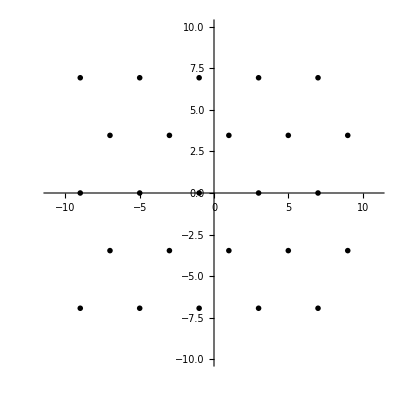

```mathematica
ListPlot[Flatten[pnts10⟦"pn"⟧,1],AspectRatio->1, PlotRange-> {{-11,11},{-10,10}},GridLines->{{-10,10},{-10√3/2,10√3/2}}]
```

#### Examples

A function to plot the points returned by fill[] will be useful:

```mathematica
ClearAll[plotPnts];
 plotPnts[pnts_]:=
     Module[{Bx=pnts⟦"Bx"⟧,By=pnts⟦"By"⟧,box},box={{-Bx, Bx}, {-By, By}};
         ListPlot[Flatten[pnts⟦"pn"⟧, 1],AspectRatio->1,PlotRange->1.1box,GridLines->box, 
                  Prolog ->{EdgeForm[Dashed],LightBlue,Rectangle[{-Bx,-By},{Bx,By}]}]]
```

The returned values of the first element are the density, the spacing, number of rows and columns, and Bx & By.

```mathematica
pnts256=fill[Bx[256, 1/π],256];
pnts256⟦{"ρ","a","Bx","By"}⟧
```

<|ρ→1/π,a→(√(2 π))/3^(1/4),Bx→(8 √(2 π))/3^(1/4),By→4 3^(1/4) √(2 π)|>

```mathematica
3.5/pnts256⟦"a"⟧
```

1.83763

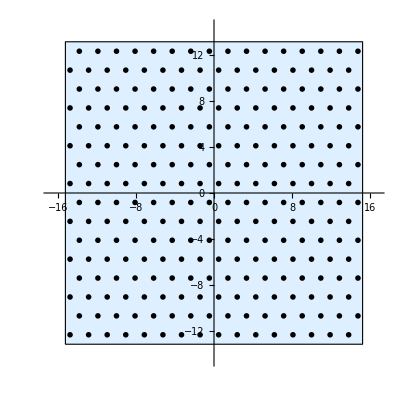

```mathematica
p256=plotPnts[pnts256]
```

Here is how to plot everything together.

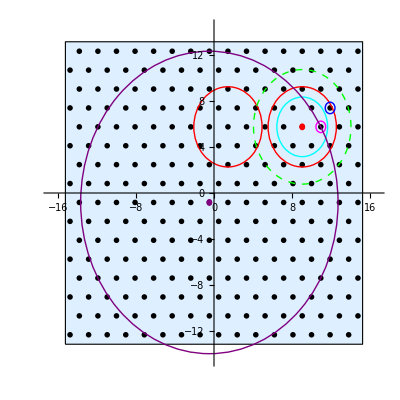

```mathematica
pnts256arr = Flatten[pnts256⟦"pn"⟧,1];
p1=pnts256arr⟦189⟧; (* Focal point *)
p2=pnts256arr⟦190⟧; (* Next point on row *)
p3=pnts256arr⟦207⟧; (* next nearest neighbor *)
p4=pnts256arr⟦189-4⟧; (* secondary shell center *)
p5=pnts256arr⟦120⟧; (* By radius center *)
Rskin = 3.5; Rshell = 5;NHOPr=1/2(1 + √3) pnts256⟦"a"⟧;
Show[p256,
Graphics[{Red,Circle[p1,Rskin],Circle[p4,Rskin],Disk[p1, 0.3],
Magenta,Circle[p2,0.5],
{Green, Dashed,Circle[p1, Rshell]},
Blue, Circle[p3,0.5],
Cyan, Circle[ p1, NHOPr],
Purple, Circle[p5, pnts256⟦"By"⟧],Disk[p5,0.3]}]]
```

Above is a 256 particle array in the defined box (light blue field encompassed by dashed line), with a focus on particle 189 (upper right plotted in red).  The red circle is the skin range of 3.5, and the green circle is the correlation range (the shell) of 5.  The magenta circled particle is one of the six nearest neighbor particles, and the blue circled particle is one of the six next nearest neighbor particles, just inside the skin. The cyan circle is the radius used to count nearest neighbors and compute the Nelson-Halperin order parameter (NHOPr, see below)[Halperin1978].  The purple circle (around the purple particle just below left center) is the radius at By (used in radial distribution calculation).

The skin range (red circles) above show that they do not overlap at four particle spacings. They could be set to 2a so that they would touch.  There would be a few more interacting particles then, and, at initialization, six particles would sit on the skin.

```mathematica
Simplify[p2-p1]
```

{(√(2 π))/3^(1/4),0}

```mathematica
Simplify[EuclideanDistance[p1,p2]]
```

(√(2 π))/3^(1/4)

```mathematica
%==a79
```

True

```mathematica
nnnd=Simplify[EuclideanDistance[p1,p3]/α79] (*next nearest neighbor distance in 1/π density interparticle distance units*)
```

√3

```mathematica
N[%]
```

1.73205

The third nearest neighbor is 2a, which is just outside the skin.

```mathematica
tnnnd=2α79
```

(2 √(2 π))/3^(1/4)

```mathematica
N[%]
```

3.80925

Particle 208 (and all the others near the green circle) lies very near the shell at 5.

```mathematica
N[pnts256arr⟦208⟧]
```

{13.8085,7.42254}

```mathematica
fnnd=Simplify[EuclideanDistance[p1,pnts256arr⟦208⟧]]
```

(√(14 π))/3^(1/4)

```mathematica
N[%]
```

5.03917

Just a hair past the shell.

##### Squaring the Box

The purple circle above shows that we could get a few more columns into the radial distribution calculation if there were a few more rows of particles. The box height is only about 87% of its width when the number of rows and columns are the same.  If there were two more rows (i.e., 18), the box dimensions would be given by setting by to the number of rows times the row height of a√3/4 (by is half of the box side):

```mathematica
Nr2=18;by288=Nr2 α79√3/4;
{16Nr2 ,by288}
```

{288,(9 3^(1/4) √π)/(√2)}

```mathematica
pnts288=fill[bx256,by288,16 18];
pnts288⟦{"ρ","a","Bx","By"}⟧
```

<|ρ→1/π,a→(√(2 π))/3^(1/4),Bx→(8 √(2 π))/3^(1/4),By→(9 3^(1/4) √π)/(√2)|>

Now the ratio of the box sides is:

```mathematica
pnts288⟦"By"⟧/pnts288⟦"Bx"⟧
```

(9 √3)/16

```mathematica
N[%]
```

0.974279

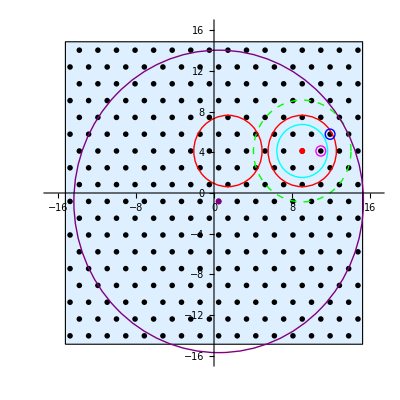

```mathematica
pnts288arr = Flatten[pnts288⟦"pn"⟧,1];
p288=plotPnts[pnts288];
p1b=pnts288arr⟦189⟧; (* Focal point *)
p2b=pnts288arr⟦190⟧; (* Next point on row *)
p3b=pnts288arr⟦207⟧; (* next nearest neighbor *)
p4b=pnts288arr⟦189-4⟧; (* secondary shell center *)
p5b=pnts288arr⟦120+17⟧; (* By radius center *)
(* Rskin = 3.5; Rshell = 5; NHOPr: These are already defined, NHOPr is unchanged *)
Show[p288,
Graphics[{Red,Circle[p1b,Rskin],Circle[p4b,Rskin],Disk[p1b, 0.3],
Magenta,Circle[p2b,0.5],
{Green, Dashed,Circle[p1b, Rshell]},
Blue, Circle[p3b,0.5],
Cyan, Circle[ p1b, NHOPr],
Purple, Circle[p5b, pnts288⟦"By"⟧],Disk[p5b,0.3]}]]
```

There are a few rules that must be observed to make the periodic boundary conditions make sense.  First, the number of rows must be even so that the top row fits properly beneath the bottom row (where it will be imaged). The number 18 was chosen sort of arbitrarily, but can be formalized as follows.  The inter-row spacing is √3/2 smaller than the column spacing, so we can have the reciprocal of that times the number of columns.  The result would need to be rounded to an integer. The table below shows a row length (number of columns), that squared, the raw increase fraction, and then the rounded number, the resulting number of particles, the box ratio, and the ration of rows to columns.

```mathematica
Table[{i,i^2,N[{2i/√3,2 i^2/√3}],N[Round[2i/√3]{1,i,(√3/2)/i,1/i}]},{i, 15,32}]//MatrixForm
```

(15 | 225 | {17.3205,259.808} | {17.,255.,0.981495,1.13333}
16 | 256 | {18.4752,295.603} | {18.,288.,0.974279,1.125}
17 | 289 | {19.6299,333.708} | {20.,340.,1.01885,1.17647}
18 | 324 | {20.7846,374.123} | {21.,378.,1.01036,1.16667}
19 | 361 | {21.9393,416.847} | {22.,418.,1.00277,1.15789}
20 | 400 | {23.094,461.88} | {23.,460.,0.995929,1.15}
21 | 441 | {24.2487,509.223} | {24.,504.,0.989743,1.14286}
22 | 484 | {25.4034,558.875} | {25.,550.,0.98412,1.13636}
23 | 529 | {26.5581,610.837} | {27.,621.,1.01664,1.17391}
24 | 576 | {27.7128,665.108} | {28.,672.,1.01036,1.16667}
25 | 625 | {28.8675,721.688} | {29.,725.,1.00459,1.16}
26 | 676 | {30.0222,780.578} | {30.,780.,0.99926,1.15385}
27 | 729 | {31.1769,841.777} | {31.,837.,0.994325,1.14815}
28 | 784 | {32.3316,905.285} | {32.,896.,0.989743,1.14286}
29 | 841 | {33.4863,971.103} | {33.,957.,0.985477,1.13793}
30 | 900 | {34.641,1039.23} | {35.,1050.,1.01036,1.16667}
31 | 961 | {35.7957,1109.67} | {36.,1116.,1.00571,1.16129}
32 | 1024 | {36.9504,1182.41} | {37.,1184.,1.00134,1.15625})

So some of the above violate the even number of rows rule (i = 18, 20, etc), and some are very close to square; the 16 x 18 is actually the worst.  If we have a number of particles we want to simulate, we can estimate the number of columns as √(2N/√3):

```mathematica
N[√(256√3/2)]
```

14.8897

As can be seen from the table above, a row of 15 would yield 17 rows (which is disallowed) and 255 particles. So maybe we should do a ceiling operation on the computation.

```mathematica
1024^2
```

1048576

And then we would have to search around that answer for a good number.  For example, to simulate a million (i.e., 1024^2=1048576), we would compute:

```mathematica
Ceiling[√(1024^2 √3/2)]
```

953

The table below lists the following columns: A Row length, the fractional number of rows to make a perfect square, and then a list consisting of {the rounded number of rows, the resulting particle count, the box ratio, the column/row ratio}.

```mathematica
Table[{i,N[2i/√3],N[Round[2i/√3]{1,i,(√3/2)/i,1/i}]},{i, 950,960,1}]//MatrixForm
```

(950 | 1096.97 | {1097.,1.04215×10^6,1.00003,1.15474}
951 | 1098.12 | {1098.,1.0442×10^6,0.999891,1.15457}
952 | 1099.27 | {1099.,1.04625×10^6,0.99975,1.15441}
953 | 1100.43 | {1100.,1.0483×10^6,0.99961,1.15425}
954 | 1101.58 | {1102.,1.05131×10^6,1.00038,1.15514}
955 | 1102.74 | {1103.,1.05337×10^6,1.00024,1.15497}
956 | 1103.89 | {1104.,1.05542×10^6,1.0001,1.15481}
957 | 1105.05 | {1105.,1.05749×10^6,0.999956,1.15465}
958 | 1106.2 | {1106.,1.05955×10^6,0.999816,1.15449}
959 | 1107.36 | {1107.,1.06161×10^6,0.999677,1.15433}
960 | 1108.51 | {1109.,1.06464×10^6,1.00044,1.15521})

So 953 or 954 columns get the job done. The way to work this is to figure out the rows and columns, and set bx and by accordingly to achieve the desired density.

#### Test Data

Below is data used to test the Julia MD2 routines.

```mathematica
N[fill[9,9]]
```

<|ρ→0.032075,a→6.,Nr→3.,Nc→3.,Bx→9.,By→7.79423,pn→{{{-7.5,-5.19615},{-1.5,-5.19615},{4.5,-5.19615}},{{-4.5,0.},{1.5,0.},{7.5,0.}},{{-7.5,5.19615},{-1.5,5.19615},{4.5,5.19615}}}|>

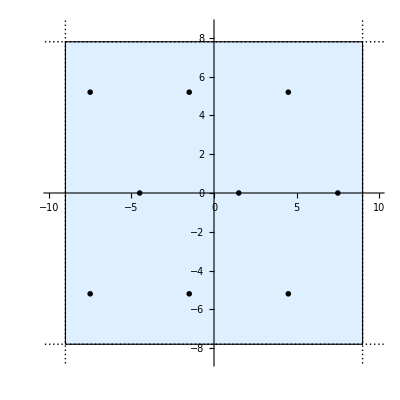

```mathematica
plotPnts[%]
```

### Angular Momentum

When applying random velocities to the particles, the velocities in the x and y directions will each be drawn from a zero-mean Gaussian distribution. The sum of velocities in the x and y direction will therefore also be zero-mean, but will have a substantial variance: for N particles, the variance will be Nσ^2.  Therefore, after initialization, we need to measure the momentum in the x and y directions and subtract that average per-particle momentum from each particle.

The same is true for angular momentum. It just won’t do for the whole system to be rotating, even a little. It is easy to measure the angular momentum. For a particle with a vector position x and vector velocity v, and particle mass m, the angular momentum about the origin is L = x × m v. In two dimensions,

```mathematica
A ={ax,ay,az};V ={vx,vy,vz};L=Cross[A,V]
```

{-az vy+ay vz,az vx-ax vz,-ay vx+ax vy}

This is very simple when the z components are zero.

```mathematica
L/.{az-> 0, vz->0}
```

{0,0,-ay vx+ax vy}

The total angular momentum is then L =∑_(i=1)^N x_i×v_i, where we assume m = 1. This can also be considered as an average rotation rate Ω, and the angular momentum can then also be expressed as L =∑_(i=1)^N r_iω =ω∑_(i=1)^N r_i, where r_i is the radial component of the particle i in cylindrical coordinates (that is, its distance from the origin). If S = ∑_(i=1)^N r_i (sort of a moment of inertia in scaled units), then the average rotation rate is given by ω = L/S, and therefore the ith particle’s share of the rotation is l_i = ω r_i.

We can calculate ω, and then say that l = ax vy - ay vx. This is insufficient to calculate a velocity vector, but the velocity vector is orthogonal to the particle vector, so their dot product will be zero.

```mathematica
Solve[l==ax vy-ay vx&&ax vx+ay vy==0,{vx,vy}]
```

{{vx→-(ay l)/(ax^2+ay^2),vy→(ax l)/(ax^2+ay^2)}}

#### Numerical Assessments

The value of S (scaled moment of inertia) is somewhat large:

```mathematica
S=Apply[Plus,Map[Norm,N[pnts256arr]]]
```

2786.81

One measurement of L was around 58. ω is then

```mathematica
58/S
```

0.0208123

```mathematica
%/(2π)
```

0.00331239

```mathematica
1/%
```

301.897

So, with that high value of L, it would take a time of almost 302, or 30,000 time steps to make a full rotation. However, only a small rotation would be a problem with the crystal interfaces at the boundaries.

The maximum range is a bit over 19:

```mathematica
Max[Map[Norm,N[pnts256arr]]]
```

19.2593

This means that even the farthest particles will only get less than 1% of the total angular momentum, but this is still more than twice what they would get if the momentum was evenly divided among the 256 particles.

```mathematica
S/%
```

144.699

### Problems with Large Number of Particles

While 256 particles was relatively straight forward, there are some issues as we try to scale to one million particles.

#### Correlation Array Length

The correlation array records all inter-particle interactions once each.  That is, if particle one interacts with particle two but not particle three, and particle two interacts with one and three, particle two’s list only includes particle three.  Interactions are limited by the the shell radius R_shell.  Since the overall density is fixed, the average number of interactions per particle is simply π ρ R_shell^2, where ρ is the density. For the 1980 system, R_shell=5 and ρ=1/π, so this number is simply 25.  With 256 particles, and each interaction only counting once, there should be no more than 255 · 25 / 2 = 3,187.5.  In fact, in 17,472 executions (of varying number of steps up to 50,000), the maximum we have observed is 3,115.  This was determined through the steps below.

home : $ cd ~/MD/Data/1980
~/MD/Data/1980 $ grep "Max number of interactions:" *.txt > MNI.txt
~/MD/Data/1980 $ R # Start R
R version 4.5 .1 (2025 - 06 - 13) -- "Great Square Root"
Copyright (C) 2025 The R Foundation for Statistical Computing
Platform : x86_ 64 - pc - linux - gnu

> td < - "/media/phil/Original/Users/phils/Documents/DSP/MD/Data/1980"
> x < - read.delim ( paste ( td, "MNI.txt", sep = "/"), ":", header = FALSE)
> max (x$V3)
[1] 3115

The current minimum the program allows (as of August 2025) is double this: N π ρ R_shell^2, where N is the number of particles (with R_shell=5 and ρ=1/π, π ρ R_shell^2=R_shell^2=25, and for N = 256,  N π ρ R_shell^2= 6,400), and the executions have been using 9,728 (N * round(1.5 * pi * density *Rshell^2)).  So, as we get to 2^20 (one million) particles, we need to have a tighter bound, and  N π ρ R_shell^2/2 would occupy about 105MB of memory (assuming 4 bytes per integer), large, but doable. A 10% margin should be added as we wouldn’t want a calculation to fail after hours of work just because this limit was too tight.

#### Correlation Algorithm

Currently, the simulation stops every 50 steps and calculates the distance between all particle pairs to create the list of those within each particle’s shell.  So particle one looks at the the distance to the other 255 particles. Particle two looks at 254, and so on.

```mathematica
Simplify[ Sum[ i, {i, 1, N-1}]]
```

1/2 (-1+N) N

So this dependence on (N^2-N)/2 can get big.

```mathematica
paircnt[N_]:=(N^2-N)/2;
Table[ {i,2^i,paircnt[2^i]}, {i,8,20,2}]
```

{{8,256,32640},{10,1024,523776},{12,4096,8386560},{14,16384,134209536},{16,65536,2147450880},{18,262144,34359607296},{20,1048576,549755289600}}

We might be able to correlate 16K particles in a reasonable amount of time (134M correlations), but the million particle system requires over a half trillion comparisons, each of which requiring two squaring operations. There are a few references of faster ways (see Kim2025, Awile2012, or Groß2019) that include divide and conquer, spatial hashing, and various tree based algorithms. Groß2019 appears closest to the amount of effort I’m willing to expend in this regard. The idea is to sort the particles by both x and y coordinates, and find those within the square grid defined by the particles position {x_i, y_i}±R_shell.  This is bigger than the circle currently used, as its size is 4R_shell^2 vs. πR_shell^2. At our density of 1/π, that is

```mathematica
N[(4 Rshell^2 - π Rshell^2)/π]
```

6.83099

almost seven extra particles.  The procedure requires two sorts, a search of the sorted list for the box limits in both lists, and then building the list of of particles in the box. We need to keep the particle interaction list in more-or-less ascending order too.  That is, particle i’s list of interacting particles should only contain particle numbers greater then i. The particles within i’s list need not be in any order.

Let’s look at the ten particle system created above as an example.

```mathematica
pnts10
```

<|ρ→1/(8 √3),a→4,Nr→5,Nc→5,Bx→10,By→5 √3,pn→{{{-9,-4 √3},{-5,-4 √3},{-1,-4 √3},{3,-4 √3},{7,-4 √3}},{{-7,-2 √3},{-3,-2 √3},{1,-2 √3},{5,-2 √3},{9,-2 √3}},{{-9,0},{-5,0},{-1,0},{3,0},{7,0}},{{-7,2 √3},{-3,2 √3},{1,2 √3},{5,2 √3},{9,2 √3}},{{-9,4 √3},{-5,4 √3},{-1,4 √3},{3,4 √3},{7,4 √3}}}|>

Here are the points.

```mathematica
p10=Flatten[pnts10⟦"pn"⟧,1]
```

{{-9,-4 √3},{-5,-4 √3},{-1,-4 √3},{3,-4 √3},{7,-4 √3},{-7,-2 √3},{-3,-2 √3},{1,-2 √3},{5,-2 √3},{9,-2 √3},{-9,0},{-5,0},{-1,0},{3,0},{7,0},{-7,2 √3},{-3,2 √3},{1,2 √3},{5,2 √3},{9,2 √3},{-9,4 √3},{-5,4 √3},{-1,4 √3},{3,4 √3},{7,4 √3}}

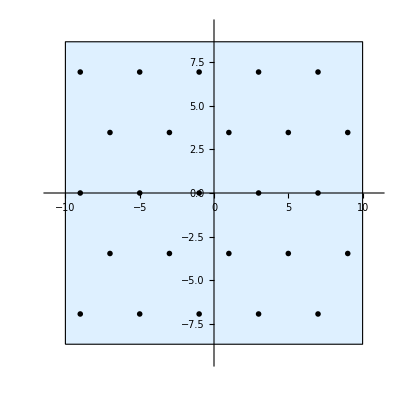

```mathematica
plotPnts[pnts10]
```

```mathematica
TableForm[p10]
```

-9 | -4 √3
-5 | -4 √3
-1 | -4 √3
3 | -4 √3
7 | -4 √3
-7 | -2 √3
-3 | -2 √3
1 | -2 √3
5 | -2 √3
9 | -2 √3
-9 | 0
-5 | 0
-1 | 0
3 | 0
7 | 0
-7 | 2 √3
-3 | 2 √3
1 | 2 √3
5 | 2 √3
9 | 2 √3
-9 | 4 √3
-5 | 4 √3
-1 | 4 √3
3 | 4 √3
7 | 4 √3

Just the x coordinates:

```mathematica
xlist=p10⟦All,1⟧
```

{-9,-5,-1,3,7,-7,-3,1,5,9,-9,-5,-1,3,7,-7,-3,1,5,9,-9,-5,-1,3,7}

a list showing their order.

```mathematica
xs=Ordering[xlist]
```

{1,11,21,6,16,2,12,22,7,17,3,13,23,8,18,4,14,24,9,19,5,15,25,10,20}

And here is the ordered list:

```mathematica
TableForm[p10⟦xs⟧]
```

-9 | -4 √3
-9 | 0
-9 | 4 √3
-7 | -2 √3
-7 | 2 √3
-5 | -4 √3
-5 | 0
-5 | 4 √3
-3 | -2 √3
-3 | 2 √3
-1 | -4 √3
-1 | 0
-1 | 4 √3
1 | -2 √3
1 | 2 √3
3 | -4 √3
3 | 0
3 | 4 √3
5 | -2 √3
5 | 2 √3
7 | -4 √3
7 | 0
7 | 4 √3
9 | -2 √3
9 | 2 √3

When we cut a swath in the x-axis of height R_shell, it will occupy an area of 2B_xR_shell.  For our 1M point example,

```mathematica
Bx1M=Bx[2^20,1/π]
```

(512 √(2 π))/3^(1/4)

```mathematica
N[%]
```

975.168

The number of particles in a swath ±R_shell wide is then:

```mathematica
N[2Bx1M Rshell/π]
```

3104.06

The number of points

```mathematica
By1M=(√3/2)Bx1M
```

256 3^(1/4) √(2 π)

```mathematica
N[%]
```

844.521

```mathematica
N[2By1M Rshell/π]
```

2688.19

We need to build the periodic boundary conditions into these results, but we’ll save that for the Julia code.  Let’s look at a particle near the middle of the array. When creating the million point system, we wrap N[] around Bx[] to cause each value to be turned into a real number, otherwise the particle list is a very long symbolic expression.

```mathematica
pnts1M=fill[N[Bx[2^20, 1/π]],2^20];
pnts1M⟦"pn"⟧⟦1⟧;
p1M=Flatten[pnts1M⟦"pn"⟧,1];
po=p1M⟦2^19-512⟧
```

{-0.476156,-0.824727}

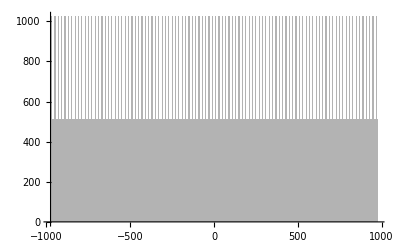

```mathematica
Histogram[p1M⟦All,1⟧,2000]
```

Those tiny peaks are the columns in which the particles line up.

```mathematica
xl1M =Ordering[p1M⟦All,1⟧];yl1M=Ordering[p1M⟦All,2⟧];
```

That appeared pretty fast. Finding a particle should be easy, as it’s position in the list should be close to

```mathematica
coor[x_,side_,K_]:=Round[(x+side)/(2side/K)]
```

```mathematica
pon=coor[po⟦1⟧,Bx1M,2^20]
```

524032

That looks about right.

```mathematica
xl1M⟦pon⟧
```

523776

```mathematica
p1M⟦%⟧
```

{-0.476156,-0.824727}

So that was exact (these particles are in their home positions).  Now let’s find the indices of particles in the x axis shell

```mathematica
po⟦1⟧+{-Rshell,Rshell}
```

{-5.47616,4.52384}

We want a list of particle numbers whose x-coordinates exist between these values. Since we already have a sorted list, we can use it.

```mathematica
pox=coor[%,Bx1M,2^20]
```

{521344,526720}

The difference between these will show us the number of elements.

```mathematica
pox⟦2⟧-pox⟦1⟧
```

5376

That’s more than we expected.

```mathematica
TableForm[p1M⟦xl1M⟦pox⟦1⟧+{-5,-4,-3,-2,-1,-0,1,2,3,4,5}⟧⟧]
```

-5.23772 | -441.229
-5.23772 | -437.93
-5.23772 | -434.631
-5.23772 | -431.332
-5.23772 | -428.033
-5.23772 | -424.734
-5.23772 | -421.436
-5.23772 | -418.137
-5.23772 | -414.838
-5.23772 | -411.539
-5.23772 | -408.24

So here is the first challenge with the technique.  We may not have found the correct limits as many elements are repeated due to particles being in home position.  We need to search from there and find the correct starting point. Again, we’ll wait until we implement in Julia for this fiddly code, and we’ll simply dither the positions a bit.

```mathematica
0.01RandomVariate[NormalDistribution[0,1],{10,2}]
```

{{-0.00129431,0.00525295},{0.00972554,0.00206169},{-0.0122528,0.000556654},{0.00844375,-0.00692277},{-0.0153076,-0.0237002},{-0.00197723,-0.00859562},{0.00379138,-0.00241316},{-0.00858791,-0.00248942},{0.00213302,-0.00645148},{-0.00488201,-0.00391364}}

```mathematica
p1Md=p1M+ 0.01RandomVariate[NormalDistribution[0,1],{Length[p1M],2}];
xl1Md =Ordering[p1Md⟦All,1⟧];yl1Md=Ordering[p1Md⟦All,2⟧];
```

The pox list doesn’t need to change, as it was simply a guess into where in the array the values would occur.

```mathematica
TableForm[p1Md⟦xl1Md⟦pox⟦1⟧+{-5,-4,-3,-2,-1,-0,1,2,3,4,5}⟧⟧]
```

-5.24535 | -365.371
-5.24534 | -216.904
-5.24511 | 515.446
-5.24509 | -167.406
-5.24506 | -378.556
-5.24506 | -91.5537
-5.24494 | 446.182
-5.24494 | 129.485
-5.24474 | -180.613
-5.24452 | 353.806
-5.24451 | -84.931

```mathematica
Clear[p1M,pnts1M,xl1M,yl1M,xl1Md,yl1Md, p1Md,p1M]
```

```mathematica
p1Mr=RandomReal[{-Bx1M,Bx1M},{2^20,2}];
xl1Mr =Ordering[p1Mr⟦All,1⟧];yl1Mr=Ordering[p1Mr⟦All,2⟧];
```

```mathematica
TableForm[p1Mr⟦xl1Mr⟦pox⟦1⟧+{-5,-4,-3,-2,-1,-0,1,2,3,4,5}⟧⟧]
```

-5.32792 | -805.659
-5.32764 | 933.182
-5.32709 | -651.35
-5.32242 | -595.726
-5.32201 | -183.104
-5.3215 | 289.871
-5.32006 | 929.364
-5.31805 | -479.694
-5.31582 | -570.5
-5.3155 | -447.413
-5.31185 | -150.872

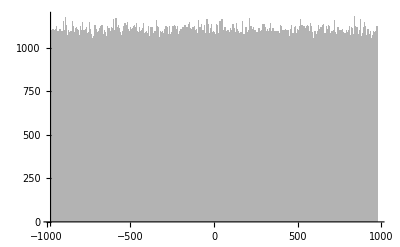

```mathematica
Histogram[p1Mr⟦All,1⟧,1000]
```

```mathematica
po=p1Mr⟦xl1Mr⟦2^19-512⟧⟧
```

{-0.773247,58.6894}

```mathematica
po⟦1⟧
```

-0.773247

```mathematica
po⟦1⟧+{-Rshell,Rshell}
```

{-5.77325,4.22675}

We want a list of particle numbers whose x-coordinates exist between these values. Since we already have a sorted list, wee can use it.

```mathematica
pox=coor[%,Bx1M,2^20]
```

{521184,526560}

The difference between these will show us the number of elements.

```mathematica
pox⟦2⟧-pox⟦1⟧
```

5376

That’s about half of what we expected.

```mathematica
TableForm[p1Mr⟦xl1Mr⟦pox⟦1⟧+{-5,-4,-3,-2,-1,-0,1,2,3,4,5}⟧⟧]
```

-5.59706 | 224.784
-5.5952 | 575.298
-5.59481 | -902.252
-5.59346 | -615.897
-5.59019 | -668.124
-5.59008 | -140.743
-5.58781 | -286.977
-5.58699 | 112.923
-5.58559 | -646.981
-5.58535 | 737.439
-5.58513 | -708.103

Below is a plot of the x-coordinates as a sorted list.

```mathematica
ListPlot[p1Mr⟦xl1Mr,1⟧]
```

-Graphics-

Timings of the current algorithm.  The log-log plot makes it look like it is linear.

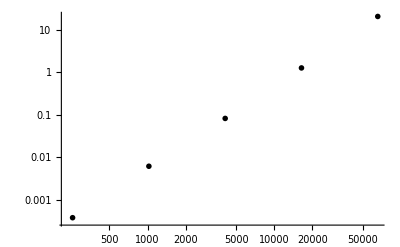

```mathematica
origtime={{256,0.00038},{1024,0.006171},{4096,0.0823},{16384,1.268},{65536,20.61}};
ListLogLogPlot[origtime]
```

This is the time per particle.

```mathematica
tpp=Apply[#2/#1&,origtime,{1}]
```

{1.48438×10^-6,6.02637×10^-6,0.0000200928,0.0000773926,0.000314484}

This is increasing on a per particle basis.

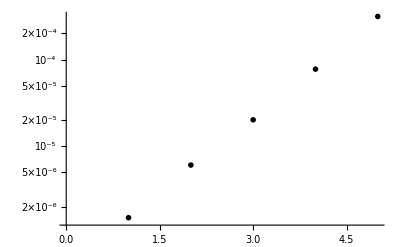

```mathematica
ListLogPlot[tpp]
```

We can quickly eliminate particles whose distance is greater than the shell (or the skin for that matter) in  either the x or y direction, and can include those whose x and y distance are both less than the 1/√2 of the shell distance.

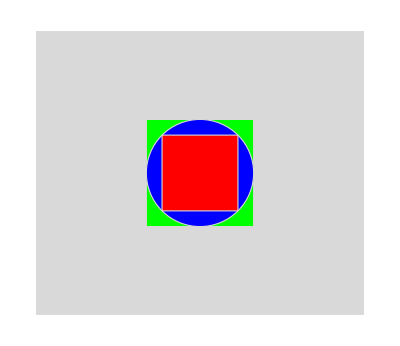

```mathematica
Graphics[{EdgeForm[Thick],LightGray,Rectangle[{-bx256, -by256},{bx256, by256}],Green, Rectangle[{-Rshell,-Rshell},{Rshell,Rshell}],Blue,Disk[{0,0},Rshell], Red,Rectangle[{-Rshell, -Rshell}/√2,{Rshell,Rshell}/√2]}]
```

The number of points in these limits at a distance of R is 4R^2/ρ for the outer square, πR^2/ρ for the circle.  The inner square’s diagonal is 2R, so  4R^2=2 x^2 and x=√2 R, and the area is 2R^2, or half the area of the green square.  If this seems odd, not that the green wide strip at the bottom is 2R wide, and (1-1/√2)R tall, and there are two, and the two vertical strips are as wide as the latter were tall, and √2 R tall.  Their area is:

```mathematica
Simplify[2(2r)(1-1/√2)r+2r(1-1/√2)√2 r]
```

2 r^2

So there is the other half.  For our current density, the average number of particles in these areas are then:

```mathematica
N[{{Green, 4 Rshell^2/π},{Blue,Rshell^2},{Red,2 Rshell^2/π}}]
```

{{RGBColor[0., 1., 0.],31.831},{RGBColor[0., 0., 1.],25.},{RGBColor[1., 0., 0.],15.9155}}

Current BaselineSpeedtest results (8/25/25):
16.915548 seconds (20.15 M allocations: 1.577 GiB, 3.27% gc time, 170 lock conflicts)

As a reminder, the times for the original algorithm are below.

```mathematica
TableForm[origtime]
```

256 | 0.00038
1024 | 0.006171
4096 | 0.0823
16384 | 1.268
65536 | 20.61

Using the above comparison based testing, the 65K run was reduced to 5.1s, a factor of four.  While hopeful, 2^18 particle (262,144) took 80.8s (per particle about four times longer than 2^16).

```mathematica
origtime = Append[ origtime, {2^18, 262.144}]
```

{{256,0.00038},{1024,0.006171},{4096,0.0823},{16384,1.268},{65536,20.61},{262144,262.144}}

With this now in the mainline CorrShell!() code, the BaselineSpeed was a bit faster:

13.940024 seconds (20.15 M allocations: 1.577 GiB, 3.52% gc time, 199 lock conflicts)

After adding inrangeq() to the GetForce!() function, we got:

13.441450 seconds (20.15 M allocations: 1.577 GiB, 3.65% gc time, 193 lock conflicts)

The first running of FastCorr!() based on sorting and searching was not a success:

julia> SpeedTest.FastCorrSpeedTest1(2^18,1/pi)
⋮
577.738706 seconds (8.14 M allocations: 664.980 GiB, 4.34% gc time)
784385

That was over seven times longer, and a lot of allocations.  There doesn’t seem to be an easy way of getting Julia to pre-allocate sets, so I’m abandoning this approach.

#### Second Correlation Algorithm

The next approach will be to divide the field into overlapping boxes of sides R_shell and spaced byR_shell. We will want at least three boxes in each dimension so b_x and b_y must both be greater thanR_shell/2and the box sides must be greater thanR_shell.  Thus the boxes will extend beyond the field. The minimum number of boxes in each direction can be found by solving the following:

```mathematica
Reduce[Rs>0&& l≥Rs&&2b>Rs&&(2n+1) l==2b &&n≥3, {n,l}]
```

b>0&&((0<Rs<(2 b)/7&&3≤n≤(2 b-Rs)/(2 Rs))||(Rs==(2 b)/7&&n==3))&&l==(2 b)/(1+2 n)

```mathematica
Clear[Kx,Ky,Lx,Ly];
N[{bx256, by256,Rshell,Kx = Floor[(bx256/Rshell) -(1/2)], Ky =  Floor[by256/Rshell-1/2], Lx =N[2bx256/(1+2Kx)],Ly =N[2by256/(1+2Ky)]}]
```

{15.237,13.1956,5.,2.,2.,6.0948,5.27825}

```mathematica
N[2bx256/Rshell]
```

6.0948

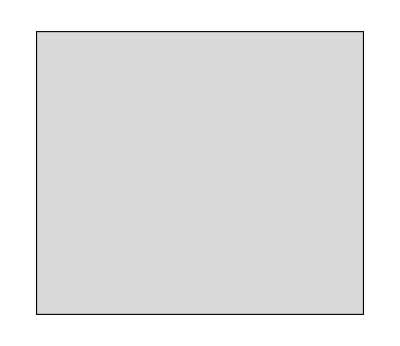

```mathematica
field256=Graphics[{EdgeForm[{GrayLevel[0], Thickness[Large]}], GrayLevel[0.85], 
  Rectangle[{-bx256, -by256}, 
   {bx256, by256}]}]
```

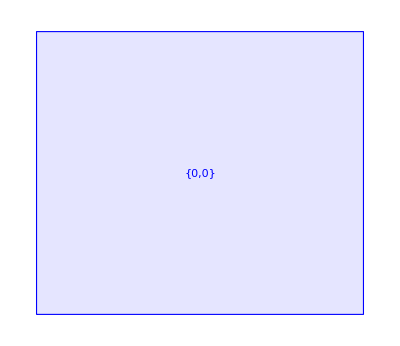

```mathematica
shellbox256=Graphics[ {EdgeForm[Thickness[Tiny]], Blue, FaceForm[Opacity[0.1]], 
  Rectangle[(1/2){-Lx, -Ly}, 
   (1/2){Lx, Ly}], Text[Style[{0,0},Tiny], {0,0}]}]
```

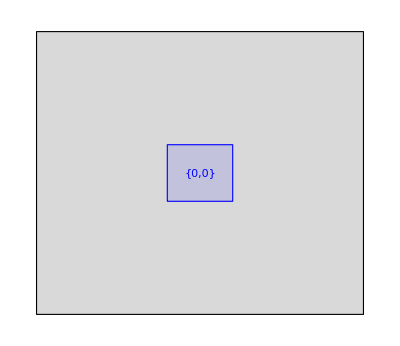

```mathematica
Show[field256,shellbox256]
```

We need a function that will plot a rectangle of a particular size with its center at a particular place and its coordinate printed at its center.

```mathematica
ClearAll[plotrect];
plotrect::usage="plotrect[{xc,yc},{lx,ly},txt] plots a rectangle centered on {xc,yc} 
with sides {lx,ly} and labeled in the center with txt."
plotrect[{xc_,yc_},{lsx_,lsy_}, txt_]:={EdgeForm[Thickness[Tiny]],Blue, FaceForm[Opacity[0.1]], 
  Rectangle[-1{lsx/2,lsy/2}+{xc,yc},{lsx/2,lsy/2}+{xc,yc}], Text[Style[txt,Tiny], {xc,yc}]}
```

plotrect[{xc,yc},{lx,ly},txt] plots a rectangle centered on {xc,yc} 
with sides {lx,ly} and labeled in the center with txt.

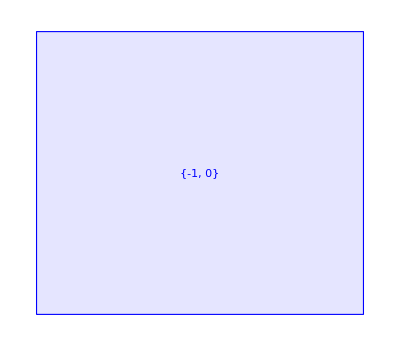

```mathematica
p3=Graphics[plotrect[{-Lx,0}, {Lx,Ly},ToString[{-1,0}]]]
```

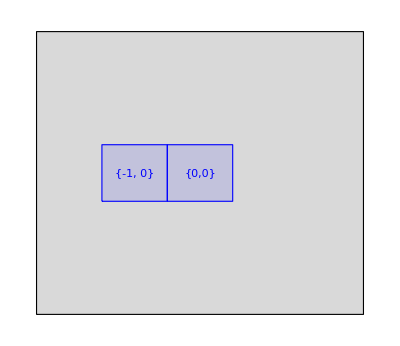

```mathematica
Show[field256, shellbox256, p3]
```

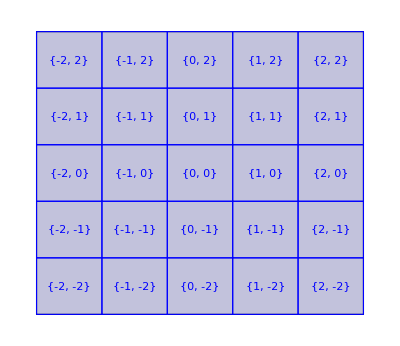

```mathematica
Show[field256,Table[Graphics[plotrect[{i Lx,j Ly},{Lx,Ly},TextString[{i,j}]]],{i,-Kx, Kx},{j,-Ky, Ky}]]
```

This creates an 5x5 array.

Now the box size is ({x,y}):

```mathematica
N[2{bx256/(2Kx+1),by256/(2Ky+1)}]
```

{6.0948,5.27825}

Which would have the following average number of particles in it.

```mathematica
Apply[Times,%]*(1/π)
```

10.24

And nine such boxes would have the following number of particles (on average):

```mathematica
9*%
```

92.16

First successful test for 65,536 particles was 0.049s, 2^18 took only 0.189s, and 2^20 was only 0.755s. 256 particles took 314μs

```mathematica
FastCorr={{256, 0.000314},{1024, 0.000917},{4096, 0.003485},{16384, 0.013133},{2^16, 0.048505},{2^18,0.189100},{2^20, 0.754521}}
```

{{256,0.000314},{1024,0.000917},{4096,0.003485},{16384,0.013133},{65536,0.048505},{262144,0.1891},{1048576,0.754521}}

julia> SpeedTest.FastCorrSpeedTest1(2^20,1/pi,shellM=25)
  0.754521 seconds
12178618

As a reminder, the original algorithm took 577s (over 9.5 minutes) for 2^18.

We can compare the original times with those of FastCorr! via the following.  This will divide each pair of numbers.

```mathematica
MapThread[#1/#2&,{origtime, Drop[FastCorr, -1]},2]
```

{{1,1.21019},{1,6.72955},{1,23.6155},{1,96.5507},{1,424.905},{1,1386.27}}

Even the 256 particle system is faster with FastCorr!.  We did not measure the original algorithm for 2^20 particles, but the per particle time was increasing by two for each doubling of the number of particles.  We estimate this below:

```mathematica
Apply[{4 #1,16#2}&,Last[origtime]]
```

{1048576,4194.3}

In minutes:

```mathematica
%⟦2⟧/60
```

69.9051

Almost 70 minutes is predicted, vs. 0.754ms with FastCorr.  Unfortunately, the baseline speedtest was longer (similar number of allocations, gc, lock & compilation time):

julia> cd(“/media/phil/Original/Users/phils/Documents/DSP/MD/dev/MD2J”)

julia> include(“./src/MD2.jl”)
MD2 included.
Main.MD2

julia> include(“./test/BaselineSpeed.jl”)

 20.994750 seconds (20.19 M allocations: 1.578 GiB, 2.90% gc time, 152 lock conflicts)

```mathematica
Share[]
```

3386880

As a final note, a similar algorithm was published by [Gross2019].

#### Nelson-Halperin Order Parameter

ψ_6=∑_(k≠j) exp i 6 θ_(j,k) /∑_(k≠j), where the sum is over all particle pairs j and k (and the i in the exponent is the
imaginary unit) and θ_(k,j) is the angle of the vector from particle k to particle j with the x axis [Halperin1978]. Note that the
angle from particle k to j is the compliment of the angle from particle j to k, so we only need to look at
each pair.

```mathematica
θ=Table[n π/3,{n,0,5}]
```

{0,π/3,(2 π)/3,π,(4 π)/3,(5 π)/3}

```mathematica
ArcTan[ Cos[θ+ϵ],Sin[θ+ϵ]]
```

{ArcTan[Cos[ϵ],Sin[ϵ]],ArcTan[Sin[π/6-ϵ],Cos[π/6-ϵ]],ArcTan[-Sin[π/6+ϵ],Cos[π/6+ϵ]],ArcTan[-Cos[ϵ],-Sin[ϵ]],ArcTan[-Sin[π/6-ϵ],-Cos[π/6-ϵ]],ArcTan[Sin[π/6+ϵ],-Cos[π/6+ϵ]]}

```mathematica
Exp[I 6 ArcTan[Tan[θ + 0.1]]]
```

{0.825336+0.564642 ⅈ,0.825336+0.564642 ⅈ,0.825336+0.564642 ⅈ,0.825336+0.564642 ⅈ,0.825336+0.564642 ⅈ,0.825336+0.564642 ⅈ}

```mathematica
Total[%]/6
```

0.825336+0.564642 ⅈ

```mathematica
Abs[%]
```

1.

Where is the point half-way between the nearest neighbors and next nearest neighbors? The next nearest neighbor to a point at {0, 0} is at {3 a /2, √3 a/2}, a distance of √3 a from {0,0}. The half-way distance between the nearest neighbors at a and the next nearest neighbors at √3 a is (√3-1)a, and adding half that distance to a yields (1+ √3 )a/2.

```mathematica
EuclideanDistance[{0, 0},{3a/2,√3 a/2}]
```

√3 Abs[a]

```mathematica
a79(1+√3)/2
```

2.60177

The number of particles expected in this radius at a density of 1/π is

```mathematica
%^2
```

6.76919

The long-range order is calculated by G_6(r)=⟨ψ_6(r)ψ_6^*(0)⟩ [Keim2007 (eq. 7), Halperin1978, Kapfer2015] where the bold r is a vector, and the ensemble average is presumed to be over all vectors of length r.  [Toledno2021, (eq. 2)] has the a similar construct: η(r)=⟨(ψ⃗)_i·(ψ⃗)_jδ(r-r_ij)⟩, where here OverVector[ψ_i] is a vector formed from the real and imaginary parts of ψ_6. This second form is nice because it is a real number, but the complex result contains more information, and its real component is equivalent to the dot product form.

The 6-fold symmetry of the hexagonal lattice means that crystal can only rotate ±30° before it starts to be closer to the baseline orientation. For example if particle i to j had a 10° angle, we would have:

```mathematica
y=10.0 Degree;
ψ=Exp[6 I y]
```

0.5+0.866025 ⅈ

The reverse has particle j to i with 180° negative angle less the 10° ( -170°), and so the result is the same.

```mathematica
y=-(180-10.0) Degree;
ψ=Exp[6 I y]
```

0.5+0.866025 ⅈ

This is so since the baseline position of each nearest neighbor is θ_i=i π/3, where i goes from 0 to 5. If a crystal is rotated by an amount -π/3 < ϕ <π/3, then 6(θ + ϕ) = i(2π) + 6ϕ which is equivalent to 6ϕ, now ranging ±2π.  When computing the total ψ_6 for each particle i, we do not need to recompute it for each particle j, merely record the same ψ for both particles.

```mathematica
Table[Exp[6 I (y+.01)],{y,0.0, 5.0*60 Degree,60 Degree}]
```

{0.998201+0.059964 ⅈ,0.998201+0.059964 ⅈ,0.998201+0.059964 ⅈ,0.998201+0.059964 ⅈ,0.998201+0.059964 ⅈ,0.998201+0.059964 ⅈ}

```mathematica
Table[6 I (y+.01)/π,{y,0.0, 5.0*60 Degree,60 Degree}]
```

{0.+0.0190986 ⅈ,0.+2.0191 ⅈ,0.+4.0191 ⅈ,0.+6.0191 ⅈ,0.+8.0191 ⅈ,0.+10.0191 ⅈ}

```mathematica
ClearAll[y,ψ,θ]
```

## Initialization

### Kinetic Energy

For the following, see Reif, pg. 249, eq. 7.5.7. The mean kinetic energy of a particle in any dimension is (1/2)kT, where k is in units of temperature per unit of energy, and T is the temperature in units defined by k. The energy of a particle of mass m = 1 is v^2/2 which can be broken into x and y components (⟨E⟩ = ⟨1/2 v_x^2+1/2 v_y^2⟩ = kT ), so that defining k = 1, each component has an expected velocity squared of T.

If we have n particles, the total energy will have a gamma distribution with α=n, and β=T. Unfortunately, Mathematica cannot figure that out.

```mathematica
TransformedDistribution[ x1^2+x2^2,{x1, x2}\[Distributed]NormalDistribution[0,T^2]]
```

TransformedDistribution[x1^2+x2^2,{x1,x2}\[Distributed]NormalDistribution[0,T^2]]

Nevertheless, we can create one for our purposes. The mean is nT, variance nT^2

```mathematica
ClearAll[ngt];
ngt[n_,T_]=GammaDistribution[n,T];
{Mean[ngt[n,T]],Variance[ngt[n,T]]}
```

{n T,n T^2}

There are some big exponents in the distribution.

```mathematica
ngt1=ngt[256,0.015];
ngtpdf1=PDF[ngt1,x]
```

Piecewise[{{2.48589×10^-38 ⅇ^(-66.6667 x) x^255, x>0}, {0, True}}]

However the mean and variance yield reasonable numbers.

```mathematica
{Mean[ngt1],Variance[ngt1]}
```

{3.84,0.0576}

The mean is simply 256 times the mean energy per particle (i.e., T).

```mathematica
%⟦1⟧/256
```

0.015

The function below will generate 2n random deviates (an x & y for each particle) with variance T, and create the sum of squares divided by two (the total kinetic energy).

```mathematica
ClearAll[ns];
ns[n_,T_]:=Apply[Plus,Map[#^2/2&,RandomVariate[NormalDistribution[0,√T],2n]]];
n0=256;T0=0.015;ns[n0,T0]
```

3.62336

The resulting energy looks like a normal distribution with mean nT and variance nT^2.

```mathematica
{n0 T0, n0 T0^2}
```

{3.84,0.0576}

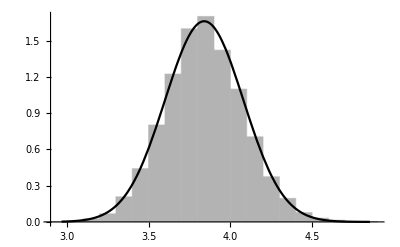

```mathematica
data=Table[ns[n0,T0],10000];
Show[Histogram[data,20,"PDF"],Plot[PDF[NormalDistribution[n0 T0,√n0 T0],x],{x,Min[data],Max[data]}]]
```

```mathematica
Through[{Mean,Variance}[data]]
```

{3.84207,0.0576996}

The recorded data is the per-particle ke, so that looks like this:

```mathematica
Through[{Mean,Variance}[data/256]]
```

{0.0150081,8.80426×10^-7}

The variance of the per particle data will be:

```mathematica
Variance[TransformedDistribution[a x,x\[Distributed]NormalDistribution[μ,σ]]]
```

σ^2 Abs[a]^2

which for our data is

```mathematica
n0 T0^2/n0^2
```

8.78906×10^-7

The relative variance of the temperature is given by

```mathematica
FullSimplify[√(n1 T1^2/n1^2)/T1, Assumptions->{n1>0, T1>0}]
```

1/(√n1)

So it only depends on the number of particles. We can plug our number in:

```mathematica
%//.n1-> n0
```

1/16

```mathematica
100N[%]
```

6.25

So around the melting temperature, there is a 6.25% standard deviation when generating data.

```mathematica
ClearAll[data];Share[]
```

408984

#### Max Motion

As explained below, the particles at a temperature T will have velocities such that the velocity squared has an expectation of T, so the velocity distribution is normal with mean zero and variance T. If there are n particles, we can discuss the maximum velocity that might be seen across four million steps (here, assuming all steps are independent). So, we assume that the n particles are independent, and each of the N steps are independent, so there are n·N possible chances for the velocity to be outside -V or V.  We would like the probability that any particle will cross the R_shell- R_skindistance in the N_skip steps between correlation runs to be small.  That velocity is either positive or negative such that (R_shell- R_skin)/(N_skipδt).  In our simulation, this speed is 1.5/(50 × 0.01) = 3 (in series 3), or 1.5/(50 × 0.0177737) = 1.6879 (in series 4). This is the two sided survival function, and at the high temperature of 0.021, has the following very small values.

```mathematica
Map[2SurvivalFunction[NormalDistribution[0,√(21/1000)],#]&,{3, 1.6879}]
```

{Erfc[10 √(15/7)],2.35966×10^-31}

```mathematica
N[%]
```

{3.3252×10^-95,2.35966×10^-31}

That is the probability that one particle is outside the envelope,  The probability that no particles are outside the envelope is 1 - p_e.  While that will be a number very close to one, we need to raise it to the power of a billion. We can approximate this using Taylor series, such that  Log[1-x]≈-x for small x. Multiplying that by the power gives us the logarithm of the probability that the event will not happen to any particle in the 4M steps.

```mathematica
256*4000000*%
```

{3.405×10^-86,2.4163×10^-22}

Of course, this is an upper limit, as it would have to sustain that velocity for 50 steps (breaking the independence criterion).

### Potential Energy

#### Potentials 1/r^n

The standard repulsive potential is given by:

```mathematica
ClearAll[rn];
rn[r_, n_]:= 1/r^n
```

Here is the form for a particular n:

```mathematica
rn[r,5]
```

1/r^5

And here are some interesting values of that.

```mathematica
test={1/2, 1, 2,a79, 3, 3.4999, 7/2, 4, nnnd α79, tnnnd};
test::usage="test = {1/2, 1, 2, a79, 3, 3.4999, 7/2, 4, nnnd α79, tnnnd}
	The explicit rationals are good test values whose results are easily done in your head (except for 7/2, which is the skin distance). α79 is the 1/π density as exact number (√(2  π/SqrtBox[3])), a79 as floating point. 3.4999 is just inside the 3.5 skin value. nnnd is the next nearest neighbor distance in a79 units, and tnnnd is the third net nearest neighbor distance (i.e., 2×a79).";
Map[ rn[#,5]&,test]
```

{32,1,1/32,0.0398981,1/243,0.00190424,32/16807,1/1024,1/(12 √2 3^(1/4) π^(5/2)),(3 3^(1/4))/(128 √2 π^(5/2))}

```mathematica
N[%]
```

{32.,1.,0.03125,0.0398981,0.00411523,0.00190424,0.00190397,0.000976563,0.00255946,0.00124681}

```mathematica
N[test]
```

{0.5,1.,2.,1.90463,3.,3.4999,3.5,4.,3.29891,3.80925}

The force is the derivative with respect to r:

```mathematica
f[r_]=D[rn[r,5],r]
```

-5/r^6

Here are the resulting forces at those same interesting values.

```mathematica
Map[f,test]
```

{-320,-5,-5/64,-0.10474,-5/729,-0.00272042,-320/117649,-5/4096,-5/(24 √3 π^3),-(15 √3)/(512 π^3)}

The skin at 3.5σ yields the following ratios to the mean separation in a hexagonal grid:

```mathematica
{rn[3.5,5]/rn[a79,5],f[3.5]/f[a79]}
```

{0.0477208,0.0259687}

The number of particles expected in a circular region of radius r is ρ π r^2, but with the density ρ = 1/π, the expected number of particles is simply r^2

```mathematica
Block[{ρ=1/π},ρ π{3.5^2,5^2}]
```

{12.25,25}

The minimum potential energy of the system on a per particle basis is the energy of six particles at a, and six more at nnnd = √3 a. Therefore the minimum potential energy per particle is half the sum of all twelve (since we ascribe half the potential energy to each pair).

```mathematica
pe=(6rn[a79,5]+6rn[nnnd a79,5])/2
```

0.127373

#### Setting the Potential to Zero at r_skin

The potential has a step in it:

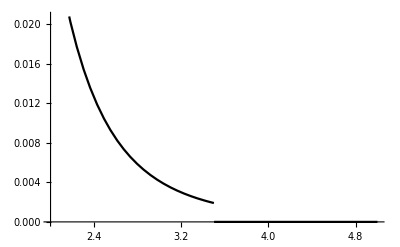

```mathematica
Plot[Piecewise[{{rn[x,5],x<3.5},{0,True}}],{x, 2, 5}]
```

However, the MD2 code has never really dealt with the step, in that the velocity of a particle crossing the step was never diminished in the direction it crossed. In effect, the step was not there, but the potential energy calculation reported it.  If rn[] was defined with the step subtracted, the force would be unchanged, but the potential would be a little lower. The step is at r = 7/2, so the excess P.E. per particle when at rest in their minimum P.E. positions is given by:

```mathematica
step=N[12rn[7/2,5]/2]
```

0.0114238

If we were to subtract that from the P.E. function rn[] the per particle P.E would be lower by (in percent):

```mathematica
100step/pe
```

8.96881

At the density of 1/π, the skin radius of 3.5 would have 12.25 particles within the skin. Of course, there are only 12 or 13 particles, never a quarter particle.  On average though there will be 12.25, so when then average per particle increase is

```mathematica
49/4rn[7/2,5]/2
```

4/343

```mathematica
N[%]
```

0.0116618

```mathematica
rn[3.5,5]
```

0.00190397

We can make a three input version of rn[] to account for the skin depth.

```mathematica
ClearAll[rn];
rn::usage="rn[r, n]=r^-n.
rn[r_, n_:5, Rskn_:3.5] respects the skin depth and causes the potential to be zero 
at the skin depth range Rskn.";
rn[r_,n_]:=r^-n;
rn[r_,n_:5,Rskn_:3.5]:=Piecewise[{{0, r≥Rskn}, {rn[r,n]-rn[Rskn,n], True}}]
```

```mathematica
?test
Print[test];Map[rn[#,5,3.5]&, test]
```

test = {1/2, 1, 2, a79, 3, 3.4999, 7/2, 4, nnnd α79, tnnnd}
	The explicit rationals are good test values whose results are easily done in your head (except for 7/2, which is the skin distance). α79 is the 1/π density as exact number (√(2  π/SqrtBox[3])), a79 as floating point. 3.4999 is just inside the 3.5 skin value. nnnd is the next nearest neighbor distance in a79 units, and tnnnd is the third net nearest neighbor distance (i.e., 2×a79).

{1/2,1,2,1.90463,3,3.4999,7/2,4,3^(1/4) √(2 π),(2 √(2 π))/3^(1/4)}

{31.9981,0.998096,0.029346,0.0379941,0.00221126,2.72019×10^-7,0,0,0.000655494,0}

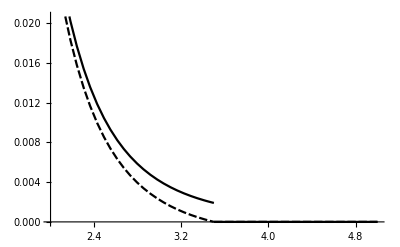

```mathematica
Plot[{Piecewise[{{rn[x,5],x<3.5},{0,True}}],rn[x,5,3.5]},{x, 2, 5}]
```

We can find the nearest points in the following way. Note that when the points are left in symbolic form, the distance returned is the square for some unknown reason, so we apply N[] to pnts256 before calling Nearest[].

```mathematica
rskin
```

rskin

```mathematica
Nearest[Flatten[N[pnts256⟦"pn"⟧],1]-> All,N[p2],{All,3.5}]
```

{<|Element→{10.9516,5.77309},Index→190,Distance→0.|>,<|Element→{9.99928,7.42254},Index→206,Distance→1.90463|>,<|Element→{11.9039,7.42254},Index→207,Distance→1.90463|>,<|Element→{12.8562,5.77309},Index→191,Distance→1.90463|>,<|Element→{9.99928,4.12364},Index→174,Distance→1.90463|>,<|Element→{9.04697,5.77309},Index→189,Distance→1.90463|>,<|Element→{11.9039,4.12364},Index→175,Distance→1.90463|>,<|Element→{10.9516,9.072},Index→222,Distance→3.29891|>,<|Element→{8.09466,7.42254},Index→205,Distance→3.29891|>,<|Element→{13.8085,7.42254},Index→208,Distance→3.29891|>,<|Element→{8.09466,4.12364},Index→173,Distance→3.29891|>,<|Element→{13.8085,4.12364},Index→176,Distance→3.29891|>,<|Element→{10.9516,2.47418},Index→158,Distance→3.29891|>}

This includes the zero distance to p2.  We need to remove p2 from the particle list.  p2 is particle 190, and we can remove it as follows:

```mathematica
Nearest[Delete[Flatten[N[pnts256⟦"pn"⟧],1],190]-> All,N[p2],{All,3.5}]
```

{<|Element→{9.99928,7.42254},Index→205,Distance→1.90463|>,<|Element→{11.9039,7.42254},Index→206,Distance→1.90463|>,<|Element→{12.8562,5.77309},Index→190,Distance→1.90463|>,<|Element→{9.99928,4.12364},Index→174,Distance→1.90463|>,<|Element→{9.04697,5.77309},Index→189,Distance→1.90463|>,<|Element→{11.9039,4.12364},Index→175,Distance→1.90463|>,<|Element→{10.9516,9.072},Index→221,Distance→3.29891|>,<|Element→{8.09466,7.42254},Index→204,Distance→3.29891|>,<|Element→{13.8085,7.42254},Index→207,Distance→3.29891|>,<|Element→{8.09466,4.12364},Index→173,Distance→3.29891|>,<|Element→{13.8085,4.12364},Index→176,Distance→3.29891|>,<|Element→{10.9516,2.47418},Index→158,Distance→3.29891|>}

Rather than work with a list of associations, we can simply ask for the distances.

```mathematica
skinlst =Nearest[Delete[Flatten[N[pnts256⟦"pn"⟧],1],190]-> "Distance",N[p2],{All,3.5}]
```

{1.90463,1.90463,1.90463,1.90463,1.90463,1.90463,3.29891,3.29891,3.29891,3.29891,3.29891,3.29891}

These can be handed to rn[] to compute the PEs as a list:

```mathematica
rn[skinlst,5]/2
```

{0.019949,0.019949,0.019949,0.019949,0.019949,0.019949,0.00127973,0.00127973,0.00127973,0.00127973,0.00127973,0.00127973}

Summing is easy:

```mathematica
pe12=Apply[Plus,%]
```

0.127373

The result is lower for the version corrected for the PE step (and this is a test value for the Julia code).

```mathematica
NumberForm[pe12o=Apply[Plus,Map[rn[#,5, 7/2]/2&,skinlst]], {11,10}]
```

0.1159487884

```mathematica
pe12-pe12o
```

0.0114238

#### Potential Function in the Field of Particles

We would like to know how the potential energy of a particle will vary as it move directly toward another particle.  We know that there are particles just outside the skin, so we must account for them by recomputing the distance to all particles as we move.

```mathematica
ClearAll[Pdx];
Pdx::usage="Pdx[p_Integer,pnts_Association,Rskn_,n_5] returns a function of {x,y} which computes the 
potential energy of particle number p moved a distance of {x, y} from its home (crystaline) position 
based on all the other particles being in their home positions with a potential function of 1/r^n and a 
range of Rskn. The function does not enforce periodic boundary conditions.";
Pdx[p_Integer,pnts_Association,Rskn_,n_:5]:= 
	Module[{pntarry=Flatten[N[pnts⟦"pn"⟧],1],point},
		point=N[pntarry⟦p⟧];
		Function[{x,y},
			Module[{dev=point+{x,y},skinlst},
			skinlst=Nearest[Delete[pntarry,p]-> "Distance",dev,{All,Rskn}];
			(*Print[skinlst];*)
			Apply[Plus, rn[#,n,Rskn]/2& /@ skinlst]]]]
```

This creates the function for particle 120 (near the center):

```mathematica
P256=Pdx[120,pnts256,Rskin]
```

Function[{x$,y$},Module[{dev$=point$12340+{x$,y$},skinlst$},skinlst$=Nearest[Delete[pntarry$12340,120]→Distance,dev$,{All,3.5}];Plus@@(1/2 rn[#1,5,3.5]&)/@skinlst$]]

Here is its use.

```mathematica
P256[3a79/2,0]
```

1.37278

We will want to mark a few particular distances, and we’ll define a function to help do that.

```mathematica
ClearAll[Vline];
Vline::usage="Vlin[x] can be used to draw a vertical line at x in a plot.  Suggested use is 
Prolog→{Directive[Gray,Dashed],Vline[x1],Vline[x2]} inside a Plot[] function call."
Vline[x_]:=Line[{Scaled[{0,-1},{x,0}], Scaled[{0,1},{x,0}]}]
```

Vlin[x] can be used to draw a vertical line at x in a plot.  Suggested use is 
Prolog→{Directive[Gray,Dashed],Vline[x1],Vline[x2]} inside a Plot[] function call.

The plot below shows the challenge.  While moving along the x-axis (line Pdx), we are moving directly toward the next particle and the energy quickly diverges, starting to grow rapidly once it gets half way (that line rides the r^5 line below x = 2).  On the other hand, as it moves along the y-axis (Pdy), the potential follows an r^-2 profile, oscillates a bit as it slips between adjacent particles, and then starts diverging as it approaches the particle two rows above. The figure includes dashed green vertical lines at a/2, a, and 3a/2, and a dotted blue line ad NHOPr.

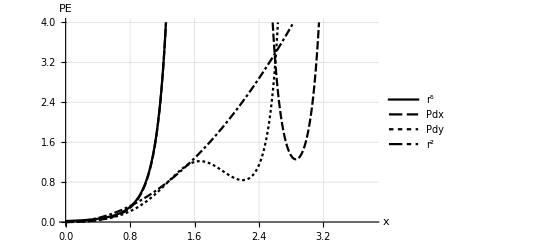

```mathematica
Plot[{rn[a79-x,5]/2,P256[x,0]-pe12o,P256[0,x]-pe12o,x^2/2},{x, 0, 2a79},
	PlotLegends->{"r^5","Pdx","Pdy","r^2"},GridLines->Automatic,
	PlotRange->{{0, 2a79},{0, 4}},AxesLabel->{x,"PE"},
	Prolog->{Directive[Green,Dashed],Vline[a79/2],Vline[a79],Vline[3a79/2],Directive[Blue,Dotted], Vline[NHOPr]}]
```

The contour plot below shows the energy (clipped to a maximum value of 2) around the center of particle 120.  The six large red circles are more-or-less centered on the adjacent particles. A black dot shows the six surrounding particles, and the black dashed lines show each surrounding particle’s NHOPr. BTW, those NHOPr lines are a distance a(√3-1)/2 from the center.

```mathematica
a79(√3-1)/2
```

0.697141

The contour plot below shows that the center of the field is relatively circular.  The black dashed lines show the NHOPr distance from each of the six surrounding particles.

```mathematica
Show[ContourPlot[Clip[P256[x,y],{0,2}],{x,-#,#},{y,-#,#},Contours->30,
	ColorFunction->Hue,PlotLegends->Automatic]&[a79],
	ListPlot[Table[a79{Cos[θ],Sin[θ]},{θ,0,2 π,π/3}]],
	Graphics[{Dashed,Table[Circle[a79{Cos[θ],Sin[θ]},NHOPr],{θ,0,2 π,π/3}]}]]
```

-Graphics-

A 3-D plot shows the valley clearly.

```mathematica
Plot3D[Clip[P256[x,y],{0,2}],{x,-#,#},{y,-#,#},ColorFunction->Hue,PlotLegends->Automatic]&[a79]
```

-Graphics3D-

So there is a broad, flat valley in which the particles move mostly freely with narrow passes that higher energy particles may approach. If we take the melting point to be at T = 0.01283, which is also the per particle kinetic energy, it is reasonable to assume that the same mean energy would find its way into potential energy.  Below we show the expected mean PE for both the transition temperature and the high fluid temp of T = 0.02, and at three times that high temperature.

```mathematica
pe12o + {0.01283, 0.02, 3*0.02}
```

{0.128779,0.135949,0.175949}

We need to zoom into the contour plot to see what the potential looks like down there.  The plot below shows that the contours are basically circular out to at least PE = 0.19.  The mean PE then can be achieved by using a circular Gaussian distribution whose standard deviation is the mean PE corresponding to the desired temperature.  We should be concerned that extreme deviations (3σ) might extend into the less circular regions of the potential, but again the plot below shows that it does not.

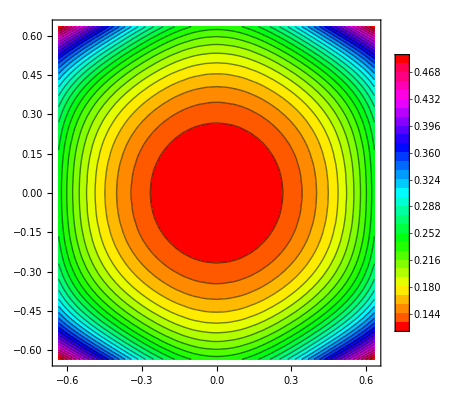

```mathematica
zcp=ContourPlot[Clip[P256[x,y],{0,2}],{x,-#,#},{y,-#,#},
Contours->30,ColorFunction->Hue,PlotLegends->Automatic]&[a79/3]
```

```mathematica
Export["zcp.pdf",zcp]
```

zcp.pdf

Below is a look at the shape of a few versions of models we might use. We see the justification for calling the PE field circular, as the Pdx and Pdy plots are nearly identical in the range of interest.  r^-2/4 does not fit very well, and the function which is the potential between two particles placed at ±a (named rn2[], defined below) appears slightly slow.  We will now plot only the excess energy.

```mathematica
ClearAll[rn2];
rn2::usage="rn2[x_,a_,n_] computes the change in potential energy of a particle with a 1/r^n potential
that is moved a distance x from its origin when there are identical particles at ±a. 
The potential at x=0 (which is the result of two interactions at a distance of a) is 
subtracted and thus rn2[0,a,n]=0.";
rn2[x_,a_,n_]:=(rn[a-x,n]+rn[a+x,n]-2rn[a,n])/2;
```

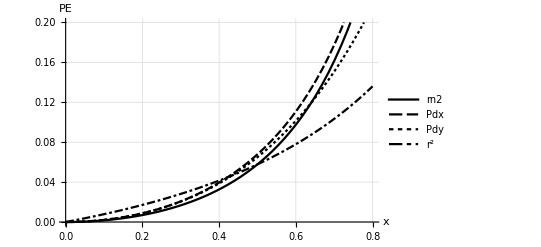

```mathematica
pz2=Plot[{rn2[x,a79,5],P256[x,0]-pe12o,P256[0,x]-pe12o,((a79-x)^-2-a79^-2)/4},{x, 0,0.8},PlotLegends->{"rn2","Pdx","Pdy","r^2"},GridLines->Automatic,AxesLabel->{x,"PE"},PlotRange->{{0, 0.8},{0, 0.2}}]
```

Pdx is 0.2 at about x = 0.72, about 38% of the inter-particle distance.

```mathematica
0.72/a79
```

0.378027

```mathematica
Export["pz2.pdf",pz2]
```

pz2.pdf

```mathematica
{pe12o,P256[0,0]/2-pe12o}
```

{0.115949,-0.0579744}

We’ll make a table of values between Pdx and Pdy.

```mathematica
tabP256=Table[{x,((P256[x,0]+P256[0,x]))/2-pe12o},{x,0,0.55,0.001}];
tabP256⟦1;;10⟧
```

{{0.,-5.96745×10^-16},{0.001,2.10631×10^-7},{0.002,8.42528×10^-7},{0.003,1.89569×10^-6},{0.004,3.37014×10^-6},{0.005,5.26589×10^-6},{0.006,7.58295×10^-6},{0.007,0.0000103213},{0.008,0.0000134811},{0.009,0.0000170623}}

```mathematica
fit=FindFormula[tabP256,x,6, RandomSeeding->4]
```

{0.21901 x^2.-0.541568 x^3.+13.0216 x^4.+1034.4 x^6.-4225.74 x^7.+10631.1 x^8.-16117.6 x^9.+13510.2 x^10.-4810.41 x^11.-152.835 Abs[x]^5.,0.219122 x^2.-0.54744 x^3.+13.1395 x^4.+1041.98 x^6.-4254.66 x^7.+10700.3 x^8.-16219. x^9.+13593. x^10.-4839.42 x^11.-154.068 Abs[x]^5.,0.218247 x^2.-0.510228 x^3.+12.4843 x^4.+1006.05 x^6.-4124.64 x^7.+10401.8 x^8.-15796.7 x^9.+13257.5 x^10.-4724.78 x^11.-147.815 Abs[x]^5.,0.218056 x^2.-0.502718 x^3.+12.3599 x^4.+999.804 x^6.-4102.74 x^7.+10352.8 x^8.-15729. x^9.+13204.8 x^10.-4707.07 x^11.-146.684 Abs[x]^5.,0.217942 x^2.-0.499369 x^3.+12.3207 x^4.+999.157 x^6.-4102.38 x^7.+10355.8 x^8.-15737.7 x^9.+13214.7 x^10.-4711.39 x^11.-146.455 Abs[x]^5.,0.219655 x^2.-0.566393 x^3.+13.4247 x^4.+1053.92 x^6.-4293.04 x^7.+10779.2 x^8.-16319.5 x^9.+13665.4 x^10.-4861.92 x^11.-156.431 Abs[x]^5.}

FindFormula[] uses some randomization, and it can be difficult to repeat results.  One very hopeful result on some prior work was a simple a+b x Tan[x], but I lost the parameters.  I added another parameter and used FindFit[] to get estimates of the parameters. In practice, the a parameter was small and negative, which give the analog a negative value for small energies, and this is of course where the function will live.  Therefor, we fit b x Tan[c x].

```mathematica
fit2=FindFit[tabP256,b x Tan[c x], {b,c},x]
```

{b→0.14406,c→1.48849}

That last equation is reasonably simple. We can also fit rn2[a x].

```mathematica
fit3=FindFit[tabP256, rn2[a x,a79,5],{a},x]
```

{a→1.05616}

That’s pretty close to one, so we’ll ignore that fit.  We can also fit the quadratic function:

```mathematica
fit4=FindFit[tabP256, a((a79-x)^-2-a79^-2),{a},x]
```

{a→0.252671}

That is pretty close to the 1/4 we were using, but we’ll plot that new function just to see it.

We can plot these results. The rn2[αx] fit is better than rn2[x], and the bxTan[cx] fit is also very good.

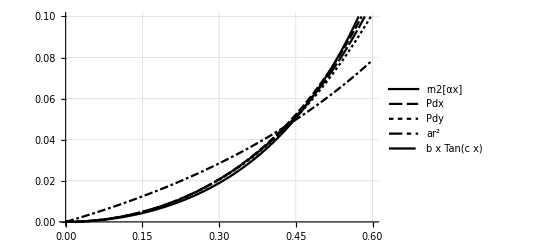

```mathematica
xTx2[x_]=b x Tan[c x]//.fit2;
f2[x_]=a((a79-x)^-2-a79^-2)//.fit4;
Plot[{rn2[1.05616x,a79,5],P256[x,0]-pe12o,P256[0,x]-pe12o,f2[x], xTx2[x]},{x, 0,0.6},PlotLegends->{"rn2[αx]","Pdx","Pdy","ar^2","b x Tan(c x)"},GridLines->Automatic,PlotRange->{{0, 0.6},{0, 0.1}}]
```

The difficulty with the xTan(x) function is that it is very specific to the density and exponent.

The mean excess PE will be equal to the mean temperature, and the highest we are interested in simulating is around T = 0.02. The distance from the minimum PE will be given by the solution to the following:

```mathematica
ScientificForm[FindRoot[xTx2[x]==0.2,{x,0.3}],15]
```

{x→7.3005266734097×10^-1}

FindRoot[] won’t work with the way Pdx[] is defined, but we can easily find it by hand.

```mathematica
{P256[0.2955,0]-(pe12o+0.02),P256[0,0.2964]-(pe12o+0.02),P256[0.294917,0]-(pe12o+0.02)}
```

{7.30325×10^-6,8.19287×10^-7,-0.00007853}

#### Initializing with Gaussian Deviations

Let’s generate 256 random points in the plane.

```mathematica
dev=RandomVariate[NormalDistribution[0,0.2955],{256,2}];
```

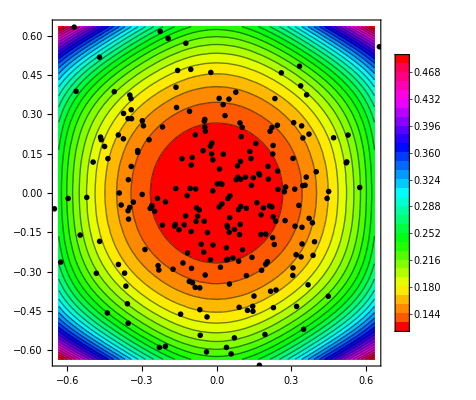

```mathematica
Show[zcp,ListPlot[dev]]
```

Find the point farthest from the center.

```mathematica
Max@@Apply[Sqrt[#1^2+#2^2]&,dev,2]
```

1.13519

Check that PE in the x, y, and diagonal direction. They are all different, as they are well outside the “circular” region.

```mathematica
{P256[#,0],P256[0,#],P256[#/√2,#/√2]}&[%]
```

{1.95124,0.706521,1.2073}

Compute the PE at each point.

```mathematica
pedev=Apply[P256,dev,2];
pedev⟦1;;10⟧
```

{0.194782,0.198012,0.1848,0.169435,0.119749,0.142591,0.121806,0.139012,0.259805,0.125146}

The max PE is large.

```mathematica
Max@@pedev
```

1.94879

However, the mean is below what we hoped for.  This is due to the wide flat bottom of the potential well.

```mathematica
{Mean[#],StandardDeviation[#]}&[pedev]
```

{0.172105,0.128378}

#### Using the Boltzmann Distribution to Initialize

Simply using a Gaussian was hoped to achieve a good-enough distribution of particles that was not starting in the odd state of passing through the minimum PE state. We turn now to the Boltzmann distribution, which states that the energy will be an exponential distribution P(E) = e^(-E/β), where β is 1/T (in scaled units).  The PE is roughly circular out to about a total PE of 0.2.  The E here is the excess PE above the minimum PE.

```mathematica
0.2-pe12o
```

0.0840512

Here is a picture of that distribution for T = 0.02.

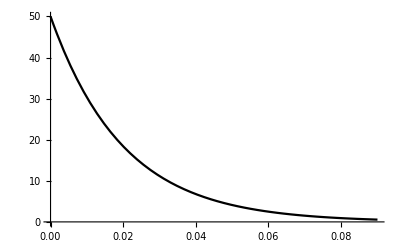

```mathematica
Plot[PDF[ExponentialDistribution[1/0.02],x],{x,0,.09}]
```

For each particle, we generate a potential energy E_0 increase from the exponential distribution, generate a random direction, and then place the particle along that direction such that its excess PE matches E_0. We would like an inverse function for that.

```mathematica
InverseFunction[xTx2[x]]
```

InverseFunction[0.14406 x Tan[1.48849 x]]

That was useless.  We can use FindRoot[] to perform the inverse for us.

```mathematica
NumberForm[FindRoot[xTx2[x]==0.2,{x,.3}], 15]
```

{x→0.73005266734097}

```mathematica
xTx2[x]-0.2/.%
```

0.

We can try to make a series and invert that.  Here is a sixth order series for xTx[]:

```mathematica
ClearAll[sxTx6];
sxTx6[x_]:=Evaluate[Normal[Series[xTx2[x],{x,0,6}]]]
```

Here, we plot its error.

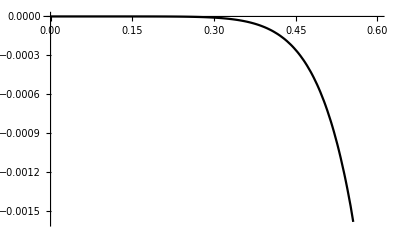

```mathematica
Plot[sxTx6[x]-xTx2[x],{x,0,0.6}]
```

And here is yet another fruitless attempt to invert it.

```mathematica
InverseSeries[sxTx6]
```

InverseSeries[sxTx6]

We can also find a formula for the inverse curve.  The very large coefficients indicate it is a poor formula.

```mathematica
invfit=FindFormula[Table[{P256[x,0],x},{x,0,0.55,0.001}],x]
```

-3764.53+168092. x-3.20164×10^6 x^2.+3.37149×10^7 x^3.-2.11965×10^8 x^4.+7.95578×10^8 x^5.-1.65065×10^9 x^6.+1.46045×10^9 x^7.

We’ll start by generating 256 samples of an exponential distribution.

```mathematica
e256=RandomVariate[ExponentialDistribution[1/0.02],256];
e256⟦1;;10⟧
```

{0.0133257,0.0138349,0.0220526,0.00574044,0.00146906,0.0514169,0.0296985,0.0124053,0.00911044,0.000454618}

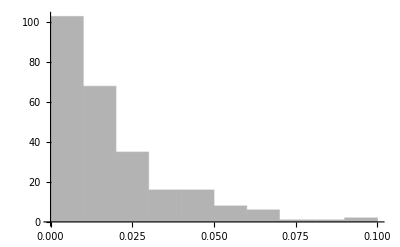

```mathematica
Histogram[e256]
```

This next expression will map them through FindRoot[] to the xTx2[] input which would have caused them (and then display the first ten).

```mathematica
r=Map[x/.FindRoot[xTx2[x]==#,{x,0.3}]& ,e256];
r⟦1;;10⟧
```

{0.243708,0.24811,0.309006,0.162017,0.0825615,0.450281,0.354153,0.235505,0.202943,0.0460085}

The histogram of that result looks more Normal than Exponential.

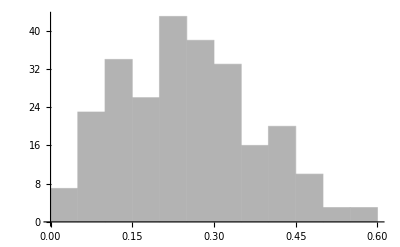

```mathematica
Histogram[r]
```

Mapping back through xTx2[] returns our exponential result.

```mathematica
Histogram[xTx2[r]]
```

-Graphics-

Now we generate 256 angles between zero and 2π.

```mathematica
angles=RandomVariate[UniformDistribution[{0,2π}],256];
angles⟦1;;10⟧
```

{4.14452,2.79265,2.58861,3.56488,4.2219,3.33575,3.00872,3.90259,1.41074,5.17805}

The expression below will will take each deviation and angle and form an {x,y} pair.

```mathematica
dev2=Thread[{#1Cos[#2],#1Sin[#2]}&[r,angles]];
dev2⟦1;;10⟧
```

{{-0.131075,-0.205459},{-0.233157,0.0848301},{-0.262953,0.162298},{-0.147718,-0.0665497},{-0.038891,-0.0728278},{-0.44182,-0.0868774},{-0.351032,0.0469187},{-0.17054,-0.162415},{0.0323441,0.200349},{0.0206584,-0.0411097}}

We can see below that the samples are more concentrated in the center than the Gaussian one was.

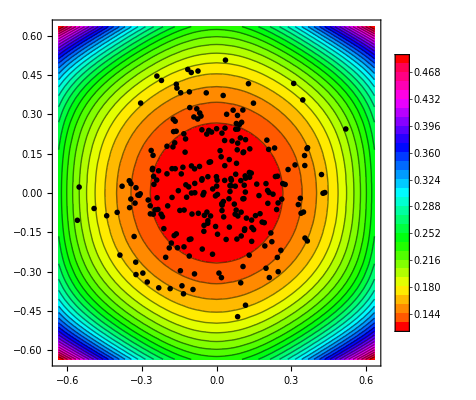

```mathematica
Show[zcp,ListPlot[dev2]]
```

Find the point farthest from the center. This is smaller than the previous result, which is often greater than one.

```mathematica
Max@@Apply[Sqrt[#1^2+#2^2]&,dev2,2]
```

0.574083

Check that PE at that displacement in the x, the y, and the diagonal direction. They are all similar, as they are well inside the “circular” region.

```mathematica
{P256[#,0],P256[0,#],P256[#/√2,#/√2]}&[%]
```

{0.213702,0.206795,0.2102}

Compute the PE at each point, and display the first ten:

```mathematica
pedev2=Apply[P256,dev2,2];
pedev2⟦1;;10⟧
```

{0.129148,0.129653,0.137824,0.121599,0.117393,0.167796,0.145791,0.128225,0.124926,0.116395}

The max PE is reasonable.

```mathematica
Max@@pedev2
```

0.209611

The mean is about what we hoped for.

```mathematica
{Mean[#],StandardDeviation[#]}&[pedev2]
```

{0.134477,0.018065}

The mean is only a bit higher than our target.

```mathematica
pe12o+0.02
```

0.135949

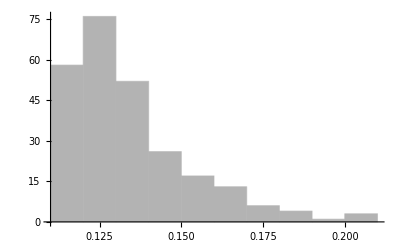

```mathematica
Histogram[pedev2]
```

In Julia, the root can be found with the Roots.jl package (note: xTx2 changed from this snapshot):

julia> xTx(x) = 0.138006 * x * tan(1.55419 * x)

julia> f(x,p) = xTx(x) - p
f (generic function with 2 methods)

julia> find_zero( f, 0.3, 0.02)
0.2949171886685355

##### Using rn2[] Instead

The xTx2[] function does not scale well, and certainly won’t work for other values of n, so we dropped back to rn2[].  Following the procedure above, we will make a one argument rn2[] function to use in Findroot[].

```mathematica
rn2a5[x_]= rn2[x,a79,5]
```

1/2 (-0.0797961+1/(1.90463-x)^5+1/(1.90463+x)^5)

```mathematica
rr=Map[x/.FindRoot[rn2a5[x]==#,{x,0.3}]& ,e256];
rr⟦1;;10⟧
```

{0.270925,0.275589,0.339018,0.182555,0.0938306,0.478684,0.384732,0.262206,0.227245,0.0524015}

The histogram of that result looks more Normal than Exponential.

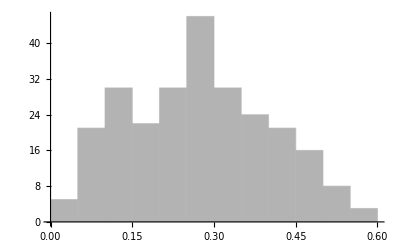

```mathematica
Histogram[rr]
```

Mapping back through rn2[] returns our exponential result.

```mathematica
Histogram[rn2[rr,a79,5]]
```

-Graphics-

The expression below will will take each deviation and angle and form an {x,y} pair.

```mathematica
dev3=Thread[{#1Cos[#2],#1Sin[#2]}&[rr,angles]];
dev3⟦1;;10⟧
```

{{-0.145713,-0.228404},{-0.25898,0.0942252},{-0.288492,0.178061},{-0.166443,-0.0749861},{-0.0441993,-0.0827683},{-0.469689,-0.0923574},{-0.381341,0.0509698},{-0.189875,-0.180829},{0.0362171,0.22434},{0.023529,-0.046822}}

We can see below that the samples are also more concentrated in the center than the Gaussian one was.

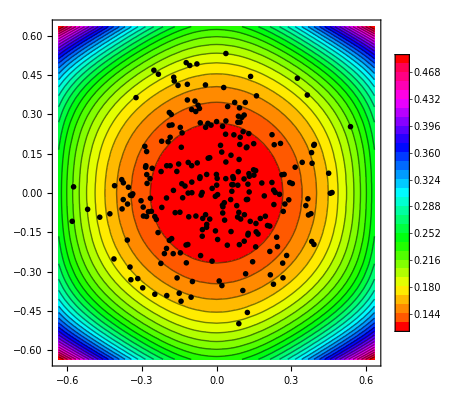

```mathematica
Show[zcp,ListPlot[dev3]]
```

Find the point farthest from the center. This is smaller than the previous result, which is often greater than one.

```mathematica
N[Sqrt[3]]
```

1.73205

```mathematica
Max@@Apply[Sqrt[#1^2+#2^2]&,dev3,2]
```

0.594983

Check that PE at that displacement in the x, the y, and the diagonal direction. They are all similar, as they are well inside the “circular” region.

```mathematica
{P256[#,0],P256[0,#],P256[#/√2,#/√2]}&[%]
```

{0.223999,0.21524,0.219565}

Compute the PE at each point, and display the first ten:

```mathematica
pedev3=Apply[P256,dev3,2];
pedev3⟦1;;10⟧
```

{0.132523,0.13308,0.142694,0.123165,0.117817,0.176055,0.151966,0.131362,0.127334,0.116528}

The max PE is reasonable.

```mathematica
Max@@pedev3
```

0.219373

The mean is about what we hoped for.

```mathematica
{Mean[#],StandardDeviation[#]}&[pedev3]
```

{0.138159,0.0205505}

The mean is only a bit higher than our target.

```mathematica
pe12o+0.02
```

0.135949

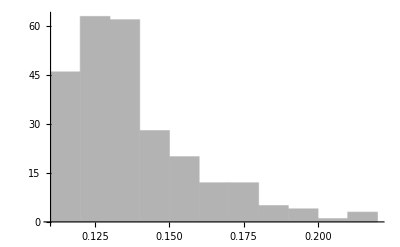

```mathematica
Histogram[pedev3]
```

```mathematica
Clear[r,rr,e256,invfit,sxTx6,dev2,dev3,xTx2,angles,zcp,pedev2,pedev3]
```

```mathematica
Share[]
```

4283704

## Other Topics

### Pair Distribution Function

The exact pair distribution function is a sum of Dirac delta functions based on the particle location:

g(r) = 1/(2N)∑_(i=1)^(N-1) ∑_(j=i+1)^N ⟨δ(|r_ij|-r)⟩

where N is the number of particles, r_ijis the vector between particles i & j, and the angle brackets indicate the expectation or average. In our simulation system, we can compute this directly, but this isn’t really useful, as g(r) is zero everywhere but where there are particles. With a small number of particles, we would not expect this function to “fill in” the gaps.

If we discretize r such that an array r[i] has the number of points found between (i-1)δr < r < i δr, we might find a useful function.We can walk over all particle pairs as above, but increment r[Floor[|r_ij|/δr]+1] (that is, if the ratio is less than one, increment the first location, and so on).

Recall that the fill[] function will place particles in a grid and return an association of the main parameters. We will use the “Bx”, “By”, and “pn” elements, the x and y box lengths and the particles themselves. First, we need to establish periodic boundary conditions.

```mathematica
ClearAll[pbc];
pbc::usage="pbc[{x,y},Bx,By] will return a pair {xi,yi} that obey the 
periodic boundary conditions on Bx and By.}";
pbc[x_,B_]:=If[Abs[x]<=B,0,Sign[x]2B];
pbc[{x_,y_},Bx_,By_]:={x-pbc[x,Bx],y-pbc[y,By]}
```

Here is an example:

```mathematica
{12-pbc[12,7],pbc[{-15,13},14,12]}
```

{-2,{13,-11}}

Now we can define the function.

```mathematica
ClearAll[gc];
gc::usage="gc[pa,Ng] returns a length Ng array r such that r[i] contains the 
number of particles of pa that are within iz/Ng distance from each other, 
where z is the smaller of the Bx or By distances.";
gc[pa_,Ng_]:=Module[{r=Table[0,Ng],Bx=N[pa["Bx"]],By=N[pa["By"]],pn=N[Flatten[pa["pn"],1]],
					dr,Np,c,v,vp,nv},
	dr=Min[ Bx, By]/Ng; (* This is the max Range *)
	Print[{Bx,By,dr}];
	Np=Length[pn];
	Do[c=Floor[(nv=Norm[vp=pbc[v=pn⟦j⟧-pn⟦i⟧,Bx,By]])/dr]+1;
	   If[c≤Ng,r⟦c⟧+=1(*;
		If[And[i<3,j<18],Print[{i,j,v,vp,nv,c}]]*),0],
	   {i,1,Np-1},{j,i+1,Np}];
	r]
```

Here is an example with all of the particles in their home positions.

```mathematica
N[Norm[pnts256arr⟦2⟧-pnts256arr⟦1⟧]]
```

1.90463

```mathematica
gr1=gc[pnts256,100]
```

{15.237,13.1956,0.131956}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,768,0,0,0,0,0,0,0,0,0,186,582,0,0,768,0,0,0,0,0,0,0,0,0,1536,0,0,0,0,768,0,0,0,0,0,54,714,0,1536,0,0,0,0,768,0,0,0,0,1536,0,0,0,1536,0,0,0,0,0,768,0,48,720,1536,0,0,0,1536,0,0,0,0,0,768,1536,0,0,1536,0,0,0,1536,0,0,0,0,18}

We can see the total number of interactions within the useable range by summing the list:

```mathematica
Plus@@gr1
```

20754

This is less than the total of all pairs (particle one pairs with the next 255, particle two with the next 254, and so on):

```mathematica
{Sum[i,{i,1,255}],255*(255+1)/2, n(n+1)/2//.n->255}
```

{32640,32640,32640}

The y axis is the shorter, so at a density of 1/π, the expected number of particles in this radius is

```mathematica
pnts256["By"]^2
```

32 √3 π

Which evaluates to

```mathematica
N[%]
```

174.125

Each iteration is over n-1 particles, so this evaluates to

```mathematica
n(n+1)/2//.n->%-1
```

15072.6

This is below what we observed.  We can go backward and see how many particles might have been paired.

```mathematica
Solve[n(n+1)/2==(Plus@@gr1-1),n]
```

{{n→1/2 (-1-5 √6641)},{n→1/2 (-1+5 √6641)}}

```mathematica
N[%]
```

{{n→-204.231},{n→203.231}}

```mathematica
pnts256["By"]/pnts256["a"]
```

4 √3

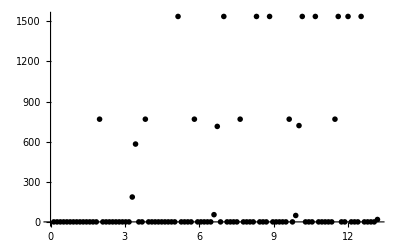

```mathematica
ListPlot[Table[{0.131956i,gr1⟦i⟧},{i,1,100}]]
```

Plot of the counts in g(r) for the 256 point system with particles sitting in their home positions.

It was a bit of surprise that the maximum was so far right, but that does make some sense in that each δr covers a bigger swath. The area of an infinitesimal swath of width δr at range r is given by the derivative of the area of a circle of radius r:

```mathematica
D[π r^2,r]
```

2 π r

The actual width for our finite swatch is simply the difference in the areas. Here, r is not continuous but takes discrete values given by r_i=i δr, and the swath at r_i takes in all particles found between (i -1)δr and  i δr.

```mathematica
Simplify[π (δr i)^2-π(δr (i-1))^2]
```

(-1+2 i) π δr^2

To use this, we need to divide each element by the above values, and also the number of particles over which we take the average. Since we do not count each interaction twice,we will divide by N/2 instead of N.

```mathematica
ClearAll[g];
g::usage="g[pa,Ng] returns a length Ng array r such that r[i] contains the 
avereage number of particles per unit area of pa that are within iz/Ng distance from each 
other, where z is the smaller of the Bx or By distances.";
g[pa_,Ng_]:=Module[{r=gc[pa, Ng],drs=N[(pa["By"]/Ng)^2],Np=Length[Flatten[pa["pn"],1]]},
	Table[2r⟦i⟧/(Np drs π(2i-1)),{i, Ng}]]
```

{15.237,13.1956,0.131956}

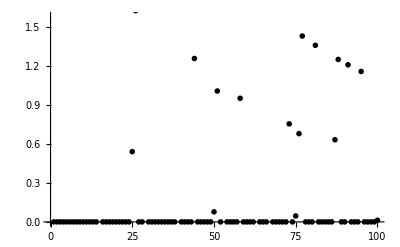

```mathematica
ListPlot[g[pnts256,100]]
```

```mathematica
rpnt256=pnts256;
rpnt256["pn"]=Module[{Bx=N[pnts256["Bx"]],By=N[pnts256["By"]]},{Transpose[{RandomReal[{-Bx,Bx},256],RandomReal[{-By,By},256]}]}];
g[rpnt256,100]
```

{15.237,13.1956,0.131956}

{0.571268,0.428451,0.314197,0.265231,0.158685,0.298617,0.439437,0.25707,0.285634,0.172884,0.380845,0.335309,0.354186,0.280344,0.315182,0.336311,0.337567,0.346841,0.262474,0.325916,0.355301,0.292276,0.279286,0.395026,0.282719,0.327639,0.247909,0.360937,0.278117,0.314681,0.290316,0.294702,0.301014,0.289897,0.337379,0.36006,0.311067,0.298963,0.296762,0.319982,0.329713,0.297679,0.267152,0.303691,0.330565,0.304467,0.28717,0.321714,0.306247,0.331797,0.323813,0.314752,0.323718,0.319002,0.323631,0.338386,0.309647,0.357663,0.345446,0.320438,0.313961,0.282151,0.318767,0.340736,0.307776,0.339054,0.294224,0.294097,0.304398,0.344199,0.34033,0.325583,0.313212,0.307008,0.340269,0.301713,0.316438,0.32894,0.309285,0.335036,0.290956,0.345214,0.293424,0.326683,0.284789,0.323217,0.312051,0.299507,0.324364,0.310368,0.330609,0.343385,0.310337,0.313128,0.326439,0.318534,0.348532,0.303211,0.316082,0.315776}

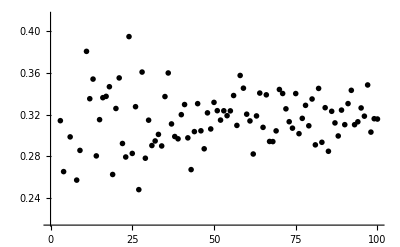

```mathematica
ListPlot[%]
```

And this is tending toward the density.

```mathematica
N[1/π]
```

0.31831

### Particle Propagation

#### Verlet Algorithm

The initial design used the Verlet algorithm [Verlet1967]. This starts with the following simple statements:
1) r_(n+1)= r_n + v_nδt + 1/2a_nδt^2

This is perfectly reasonable from a constant acceleration perspective, or from a Taylor series perspective.  Also, if the velocity was reversed, we would get the following:
2) r_(n-1)= r_n - v_nδt + 1/2a_nδt^2

Adding these two equations, we get

3) r_(n+1)=2 r_n-r_(n-1)+a_n δt^2.

If the potential was given by the rn2[] function, the force is its derivative.

Here is rn2[] :

```mathematica
rn2[x,a,n]
```

1/2 (-2 a^-n+(a-x)^-n+(a+x)^-n)

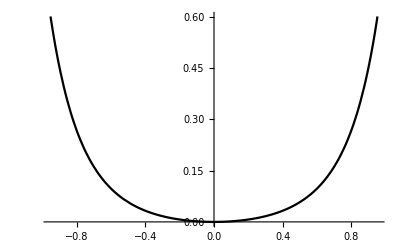

```mathematica
Plot[rn2[x,a79,5],{x,-a79/2,a79/2}]
```

Here is a function of the resulting force:

```mathematica
f[x_,a_,n_]=-Dt[rn2[x,a,n],x,Constants->{a,n}]
```

1/2 (-n (a-x)^(-1-n)+n (a+x)^(-1-n))

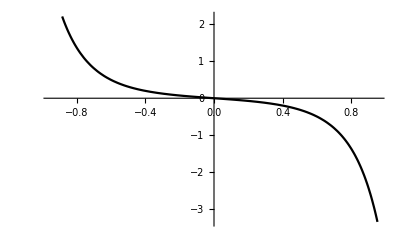

```mathematica
Plot[f[x,a79,5],{x,-a79/2,a79/2}]
```

Let’s say that the particle is moving fast to the left (negative velocity) of -0.6 (hot run of S4.0021 max speed) at -a79/2 (that is, it is quite near a particle).

```mathematica
Verlet[p_,v_, dt_]:=Module[
	{a=f[p,a79,5](*acceleration at time n*), pnm1,pen,ken,ten,pnp1,vnp1,kenp1,penp1,tenp1},
	pnm1=p-v*dt(*position at step n - 1*);
	pen=rn2[p,a79,5](* potential energy at step n*);
	ken=(1/2)v^2(* kinetic energy at step n for unity mass*);
	ten=pen+ken(* total energy at step n*);
	pnp1=2p-pnm1+a dt^2(* position at step n + 1*);
	vnp1=(pnp1-p)/dt (* velocity at step n+1 *);
	kenp1=(1/2)vnp1^2;
	penp1=rn2[pnp1,a79,5];
	tenp1=kenp1+penp1;
	<|"pn"->p,"pnm1"->pnm1,"pen"->pen,"ken"->ken,"ten"->ten,"pnp1"->pnp1,"vnp1"->vnp1,"kenp1"->kenp1,
	"penp1"->penp1,"tenp1"->tenp1,"dte%"->100(tenp1-ten)/ten|>]
```

```mathematica
dt1=0.0177737;(* time step*)
vn=-0.6; (* velocity at step n*)
pn=-a79/2; (* position at step n*)
(s1=Verlet[pn,vn,dt1](* step 1*))
```

<|pn→-0.952313,pnm1→-0.941649,pen→0.601098,ken→0.18,ten→0.781098,pnp1→-0.96192,vnp1→-0.54051,kenp1→0.146076,penp1→0.634251,tenp1→0.780327,dte%→-0.0987344|>

So, the particle was nearly stopped: its final position is very near it’s initial position.

```mathematica
(s2=Verlet[s1["pnp1"],s1["vnp1"],dt1])
```

<|pn→-0.96192,pnm1→-0.952313,pen→0.634251,ken→0.146076,ten→0.780327,pnp1→-0.970403,vnp1→-0.477282,kenp1→0.113899,penp1→0.665262,tenp1→0.779161,dte%→-0.14935|>

That almost a 0.15% drop in total energy. One more step:

```mathematica
(s3=Verlet[s2["pnp1"],s2["vnp1"], dt1])
```

<|pn→-0.970403,pnm1→-0.96192,pen→0.665262,ken→0.113899,ten→0.779161,pnp1→-0.977699,vnp1→-0.410524,kenp1→0.0842649,penp1→0.693323,tenp1→0.777588,dte%→-0.201919|>

Now we’ve lost 0.2%. We can look at the overall result of three steps:

```mathematica
100(s3["tenp1"]-s1["ten"])/s1["ten"]
```

-0.449355

We can see that the loss is accelerating.  Now this is the opposite of the effect we saw in the series 4 runs, where the total energy grew after about a million steps.

The other extreme is when the particle is moving fast, but at position zero.

```mathematica
(s1b=Verlet[0,vn, dt1])
```

<|pn→0,pnm1→0.0106642,pen→0.,ken→0.18,ten→0.18,pnp1→-0.0106642,vnp1→-0.6,kenp1→0.18,penp1→0.0000187649,tenp1→0.180019,dte%→0.0104249|>

```mathematica
(s2b=Verlet[s1b["pnp1"],s1b["vnp1"],dt1])
```

<|pn→-0.0106642,pnm1→0.,pen→0.0000187649,ken→0.18,ten→0.180019,pnp1→-0.0213273,vnp1→-0.599937,kenp1→0.179962,penp1→0.0000750846,tenp1→0.180038,dte%→0.0104358|>

```mathematica
(s3b=Verlet[s2b["pnp1"],s2b["vnp1"],dt1])
```

<|pn→-0.0213273,pnm1→-0.0106642,pen→0.0000750846,ken→0.179962,ten→0.180038,pnp1→-0.0319882,vnp1→-0.599812,kenp1→0.179887,penp1→0.000169035,tenp1→0.180056,dte%→0.0104607|>

```mathematica
100(s3b["tenp1"]-s1b["ten"])/s1b["ten"]
```

0.0313247

Now we will cut the time step to 0.01.  The worst error was in the high potential energy position.

```mathematica
dt2=0.01;
(s1c=Verlet[pn,vn, dt2])
```

<|pn→-0.952313,pnm1→-0.946313,pen→0.601098,ken→0.18,ten→0.781098,pnp1→-0.957978,vnp1→-0.566529,kenp1→0.160478,penp1→0.620404,tenp1→0.780882,dte%→-0.0276982|>

```mathematica
(s2c=Verlet[s1c["pnp1"],s1c["vnp1"],dt2])
```

<|pn→-0.957978,pnm1→-0.952313,pen→0.620404,ken→0.160478,ten→0.780882,pnp1→-0.963296,vnp1→-0.531836,kenp1→0.141425,penp1→0.639171,tenp1→0.780596,dte%→-0.036645|>

```mathematica
(s3c=Verlet[s2c["pnp1"],s2c["vnp1"],dt1])
```

<|pn→-0.963296,pnm1→-0.953844,pen→0.639171,ken→0.141425,ten→0.780596,pnp1→-0.971615,vnp1→-0.46805,kenp1→0.109535,penp1→0.669835,tenp1→0.779371,dte%→-0.156912|>

```mathematica
100(s3c["tenp1"]-s1c["ten"])/s1c["ten"]
```

-0.221144

That’s a 0.22% drop in total energy. Finally, let’s try double the speed.  It was interesting that the force at a79/2 was enough to essentially stop the particle.  What happens if the force is not enough is not enough to stop the particle?

```mathematica
s1d=Verlet[pn,2vn, dt1];
s2d=Verlet[s1d["pnp1"],s1d["vnp1"],dt1];
s3d=Verlet[s2d["pnp1"],s2d["vnp1"],dt1];
{s1d,s2d,s3d,100(s3d["tenp1"]-s1d["ten"])/s1d["ten"]}
```

{<|pn→-0.952313,pnm1→-0.930984,pen→0.601098,ken→0.72,ten→1.3211,pnp1→-0.972584,vnp1→-1.14051,kenp1→0.650382,penp1→0.673513,tenp1→1.32389,dte%→0.211652|>,<|pn→-0.972584,pnm1→-0.952313,pen→0.673513,ken→0.650382,ten→1.32389,pnp1→-0.991652,vnp1→-1.07281,kenp1→0.575458,penp1→0.750831,tenp1→1.32629,dte%→0.18089|>,<|pn→-0.991652,pnm1→-0.972584,pen→0.750831,ken→0.575458,ten→1.32629,pnp1→-1.00936,vnp1→-0.996153,kenp1→0.49616,penp1→0.831849,tenp1→1.32801,dte%→0.129654|>,0.523088}

Here we see the energy grow by 0.52% after three steps.

#### Velocity Verlet

This algorithm claims to be more accurate (from the wayback machine: (https://web.archive.org/web/20211023234749/https://embnet.vital-it.ch/MD_tutorial/pages/MD.Part1.html, that’s the 23 October 2021: “20211023”). It is a two step process:
r_(n+1) = r_n + v_nδt + a_nδt^2/2
v_(n+1) = v_n + (a_n + a_(n+1))δt/2

This may not take more computer time because we compute the velocity at each step of the Verlet process anyway.

Going back to the original paper describing the velocity Verlet [Swope1982] we see the derivation of the algorithm.  Swope defines z_n=(r_(n+1)-r_n)/ δt (a velocity sometime between n and n+1), and substitutes equation 3 above (r_(n+1)=2 r_n-r_(n-1)+a_n δt^2, eq. A3 in Swope) into the r_(n+1) term of z_n.

z_n=(2 r_n-r_(n-1)+a_n δt^2-r_n)/ δt

=(r_n-r_(n-1))/δt+a_n δt

=z_(n-1)+a_n δt

Going back to the original definition of z_n, we can simply rearrange that definition to get

r_(n+1)=r_n+z_n δt

What have we accomplished here? The update to the positions also updates the velocity, and in the velocity Verlet that update is scaled by δt instead of δt^2.

```mathematica
VVerlet[p_,v_, dt_]:=Module[
	{an=f[p,a79,5](*acceleration at time n*),
	 pen=rn2[p,a79,5](* potential energy at step n*),
	 ken=v^2/2(* kinetic energy at step n for unity mass*),
	 anp1,ten,pnp1,vnp1,kenp1,penp1,tenp1},
	ten=pen+ken(* total energy at step n*);
	pnp1=p+v*dt+an*dt^2/2(* position at step n + 1*);
	anp1=f[pnp1,a79,5] (*acceleration at n+1*);
	vnp1=v+(an+anp1)dt/2 (* velocity at step n+1 *);
	kenp1=vnp1^2/2;
	penp1=rn2[pnp1,a79,5];
	tenp1=kenp1+penp1;
	<|"pn"->p,"pen"->pen,"ken"->ken,"ten"->ten,"pnp1"->pnp1,
	  "vnp1"->vnp1,"kenp1"->kenp1,
	  "penp1"->penp1,"tenp1"->tenp1,"dte%"->100(tenp1-ten)/ten|>]
```

We will test this with the double speed data:

```mathematica
s1e=VVerlet[pn,2vn, dt1];
s2e=VVerlet[s1e["pnp1"],s1e["vnp1"],dt1];
s3e=VVerlet[s2e["pnp1"],s2e["vnp1"],dt1];
{s1e,s2e,s3e,100(s3e["tenp1"]-s1e["ten"])/s1e["ten"]}
```

{<|pn→-0.952313,pen→0.601098,ken→0.72,ten→1.3211,pnp1→-0.973113,vnp1→-1.13629,kenp1→0.645575,penp1→0.67553,tenp1→1.32111,dte%→0.000553199|>,<|pn→-0.973113,pen→0.67553,ken→0.645575,ten→1.32111,pnp1→-0.992705,vnp1→-1.06373,kenp1→0.565758,penp1→0.755389,tenp1→1.32115,dte%→0.00313942|>,<|pn→-0.992705,pen→0.755389,ken→0.565758,ten→1.32115,pnp1→-1.01093,vnp1→-0.981564,kenp1→0.481734,penp1→0.839497,tenp1→1.32123,dte%→0.00638538|>,0.0100783}

That is a 0.01% increase of total energy for three steps of the velocity Verlet, vs. the 0.52% increase for the regular Verlet algorithm. Even at ten times the velocity, we get reasonable performance.

```mathematica
s1f=VVerlet[pn,10vn,dt1];
s2f=VVerlet[s1f["pnp1"],s1f["vnp1"],dt1];
s3f=VVerlet[s2f["pnp1"],s2f["vnp1"],dt1];
{s1f,s2f,s3f,100(s3f["tenp1"]-s1f["ten"])/s1f["ten"]}
```

{<|pn→-0.952313,pen→0.601098,ken→18.,ten→18.6011,pnp1→-1.05843,vnp1→-5.90977,kenp1→17.4627,penp1→1.1147,tenp1→18.5774,dte%→-0.127311|>,<|pn→-1.05843,pen→1.1147,ken→17.4627,ten→18.5774,pnp1→-1.16239,vnp1→-5.71645,kenp1→16.3389,penp1→2.18147,tenp1→18.5204,dte%→-0.307136|>,<|pn→-1.16239,pen→2.18147,ken→16.3389,ten→18.5204,pnp1→-1.26163,vnp1→-5.26925,kenp1→13.8825,penp1→4.51086,tenp1→18.3934,dte%→-0.685712|>,-1.11679}

That’s a 1.1% delta of total energy over three steps.

### Velocity Distribution

The temperature is defined by  ⟨E⟩ = 1/2 m ⟨v_x^2⟩+1/2 m ⟨v_y^2⟩=k_b T.  In our units, m and k_b are one.  The other useful fact is that the velocities are Gaussian distributed with zero mean and

### Isobar and Isotherm

```mathematica
Solve[ρ1 T1^(2/n)==ρ2 T2^(2/n)&&P1/(ρ1 T1)==P2/(ρ2 T2)&&n>=1, {ρ2, T2}, Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[T1^(2/n) ρ1==T2^(2/n) ρ2&&P1/(T1 ρ1)==P2/(T2 ρ2)&&n≥1,{ρ2,T2},ℝ]

We know n, so plug in 5.

```mathematica
Solve[ρ1 T1^(2/5)==ρ2 T2^(2/5)&&P1/(ρ1 T1)==P2/(ρ2 T2), {ρ2, T2}, Reals]
```

{{ρ2→ConditionalExpression[(T1^(2/5) ρ1)/(Root[-P2^5 T1^3+P1^5 #1^3&,1]^(2/5)),(P1>0&&P2>0&&T1>0)||(P1<0&&P2<0&&T1>0)],T2→ConditionalExpression[Root[-P2^5 T1^3+P1^5 #1^3&,1],(P1>0&&P2>0&&T1>0)||(P1<0&&P2<0&&T1>0)]}}

That looked like it worked, but the Root expression is not simple to work with.  Let’s try a list of equations.

```mathematica
Solve[{ρ1 T1^(2/n)==ρ2 T2^(2/n),P1/(ρ1 T1)==P2/(ρ2 T2),n≥1}, {ρ2, T2}, Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{T1^(2/n) ρ1==T2^(2/n) ρ2,P1/(T1 ρ1)==P2/(T2 ρ2),n≥1},{ρ2,T2},ℝ]

How about Reduce (with constraints on T1, P1, P2, & ρ1).

```mathematica
Reduce[{ρ1 T1^(2/n)==ρ2 T2^(2/n),P1/(ρ1 T1)==P2/(ρ2 T2),n≥1,P1>0,T1>0, ρ1>0,P2>0},{ρ2, T2}, Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{T1^(2/n) ρ1==T2^(2/n) ρ2,P1/(T1 ρ1)==P2/(T2 ρ2),n≥1,P1>0,T1>0,ρ1>0,P2>0},{ρ2,T2},ℝ]

Again, let’s plug in 5 for n:

```mathematica
Reduce[{ρ1 T1^(2/5)==ρ2 T2^(2/5),P1/(ρ1 T1)==P2/(ρ2 T2),n≥1,P1>0,T1>0, ρ1>0,P2>0},{ρ2,T2},Reals]
```

n≥1&&ρ1>0&&T1>0&&P2>0&&P1>0&&ρ2==Root[-P1^2 ρ1^3+P2^2 #1^3&,1]&&T2==(P2 T1 ρ1)/(P1 ρ2)

So T2 gives us the expected result.  The new density though is the root of a third order polynomial.

```mathematica
Solve[-P1^2 ρ1^3+P2^2 x^3==0,x]
```

{{x→(P1^(2/3) ρ1)/P2^(2/3)},{x→-((-1)^(1/3) P1^(2/3) ρ1)/P2^(2/3)},{x→((-1)^(2/3) P1^(2/3) ρ1)/P2^(2/3)}}

## Special Topics

### Dislocations

#### One Moved Particle

If we move a single particle from inside one six sided cell to another, how do the particle counts change, and how much energy is required?

Below is the 288 particle system with a center particle (purple) and an adjacent cell highlighted, both with their Nelson-Halperin radii (NHOPr) drawn in cyan. The point circled in magenta will be moved down to cross both cell's NHOPr.

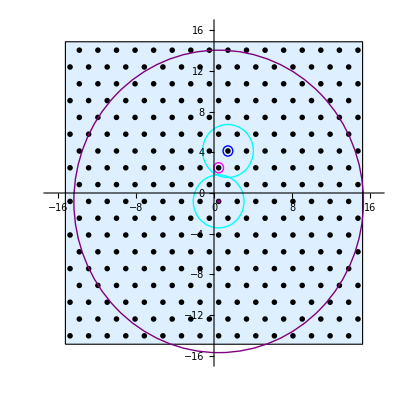

```mathematica
p2c=pnts288arr⟦10 16+9⟧; (* Row 11, col. 9; Point to move *)
p3c=pnts288arr⟦207⟧; (* next nearest neighbor *)
p4c=pnts288arr⟦11 16+9⟧; (* Row 12, col. 9; secondary shell center *)
p5c=pnts288arr⟦120+17⟧; (* By radius center *)
(* Rskin = 3.5; Rshell = 5; These are already defined*)
Show[p288,
pntsc=Graphics[{Cyan,Circle[p4c,NHOPr],
Magenta,Circle[p2c,0.5],
Blue, Circle[p4c,0.5],
Cyan, Circle[ p5c,NHOPr ],
Purple, Circle[p5c, pnts288⟦"By"⟧],Disk[p5c,0.2]}] (* Center particle *)]
```

So we want to move particle p2c (particle 169) down so it is just inside particle p5c’s NHOPr and just outside p4c’s NHOPr. Particle p2c is two rows above p1c and one half column to the right.

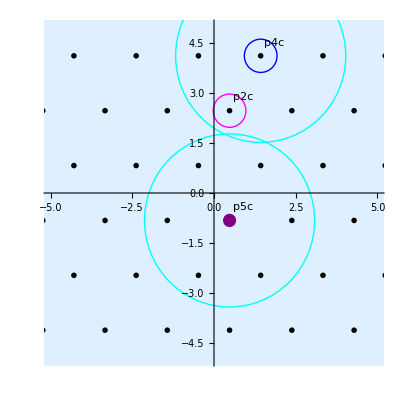

```mathematica
to={0.4,0.4};
p288245=Show[p288,pntsc, 
Graphics[{Text["p2c",p2c+to],Text["p4c",p4c+to],Text["p5c",p5c+to]}],
PlotRange->{{-5,5},{-5,5}}]
```

Finding the intersection of two circles is an algebra problem, and we can let Mathematica solve it. Below are the two points and the radius.

```mathematica
N[{p5c,p4c,NHOPr}]
```

{{0.476156,-0.824727},{1.42847,4.12364},2.60177}

Here is the equation we need to solve:

```mathematica
ss=Solve[((x-p5c⟦1⟧)^2+(y-p5c⟦2⟧)^2==NHOPr^2)&&((x-p4c⟦1⟧)^2+(y-p4c⟦2⟧)^2==NHOPr^2),{x,y}]
```

{{x→1/28 ((14 √(2 π))/3^(1/4)-3 √(14 (6-3 √3) π)),y→1/28 (14 3^(1/4) √(2 π)+√(14 (2-√3) π))},{x→1/28 ((14 √(2 π))/3^(1/4)+3 √(14 (6-3 √3) π)),y→1/28 (14 3^(1/4) √(2 π)-√(14 (2-√3) π))}}

There is an x and y coordinate for each solution:

```mathematica
MatrixForm[N[ss]]
```

(x→0.31524 | y→1.77206
x→1.58939 | y→1.52685)

We can pick out the numbers as follows: the first dimension is the row, the second is the column, and the third is the Rule[x,0.3...]. For the first point, we want row one, both columns (all), and finally the second part of the Rule[] expression.

```mathematica
pip1=N[ss]⟦1,All,2⟧;pip2=N[ss]⟦2,All,2⟧;{pip1,pip2}
```

{{0.31524,1.77206},{1.58939,1.52685}}

Below we see the two intersections plotted.  We need to move point p2c (point 169) to a spot infintesimally below pip1 (so, we move it to pip1).

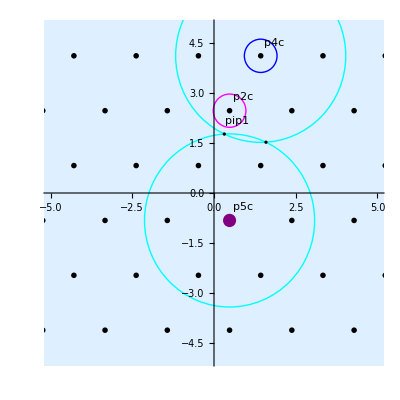

```mathematica
Show[p288245,
Graphics[{Disk[ pip1, 0.05], Disk[pip2,0.05],Text["pip1", pip1+to]}],
PlotRange->{{-5,5},{-5,5}}]
```

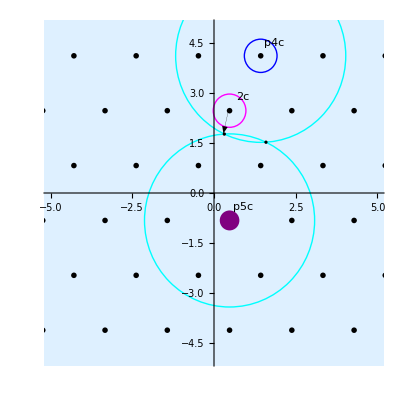

-Graphics-

The energy of moving p2c to pip1 (and no other changes) can be estimated using Pdx[], which returns a function of a vector for a chosen particle number. If we consider moving to pip1 puts p2c outside p4c’s range and moves it into p5c’s range, we have the minimum energy of such an occurrence.

```mathematica
?Pdx
```

Pdx[p_Integer,pnts_Association,Rskn_,n_5] returns a function of {x,y} which computes the 
potential energy of particle number p moved a distance of {x, y} from its home (crystaline) position 
based on all the other particles being in their home positions with a potential function of 1/r^n and a 
range of Rskn. The function does not enforce periodic boundary conditions.

We are moving particle p2c (169).

```mathematica
p5cfunc=Pdx[169,pnts288,3.5,5]
```

Function[{x$,y$},Module[{dev$=point$166946+{x$,y$},skinlst$},skinlst$=Nearest[Delete[pntarry$166946,169]→Distance,dev$,{All,3.5}];Plus@@(1/2 rn[#1,5,3.5]&)/@skinlst$]]

The potential in the home position is given by:

```mathematica
p5cfunc[0,0]
```

0.115949

Recall that this is the calculated per particle PE:

```mathematica
pe12o
```

0.115949

We need the vector distance to move p2c to get to pip1:

```mathematica
pip1-p2c
```

{-0.160916,-0.702122}

That is about 38% of the inter-particle distance, which is about the range where Pdx is circular.  Note that this displacement will move any particle to the edge of a lower right particle’s NHOPr (at the 1/π density). Here is the distance”

```mathematica
EuclideanDistance[pip1,p2c]
```

0.720326

This is about 38% of the inter-particle distance:

```mathematica
100 %/a79
```

37.8198

We use the Apply[] function (also in infix notation @@) to call the function using the above list as a parameter.

```mathematica
p5cfunc@@(pip1-p2c)-pe12o
```

0.1752

This is the total increase that a particle would, but once thermalized this will be spread among the particles.  Here is the increase in per-particle PE from the ground state in a 256 particle system:

```mathematica
(%/256)
```

0.000684376

We can look at the scenario with particle p2c actually moved, and see the NHOPr circles drawn around the moved particle. Here is the position of particle p2c (particle number 169, and it should be particle 7 in row 11):

```mathematica
{N[p2c],Floor[169/pnts288⟦"Nc"⟧+1],Mod[169,pnts288⟦"Nc"⟧], N[pnts288⟦"pn"⟧⟦11,9⟧]}
```

{{0.476156,2.47418},11,9,{0.476156,2.47418}}

To make this replacement, it is easiest to simply copy pnts288 in total, and then set the desired part to what we want.

```mathematica
pnts288p2c =pnts288; (* copy the array *)
pnts288p2c⟦"pn"⟧⟦11,9⟧=pip1; (* replace p2c coordinates with pip1 *)
N[pnts288p2c⟦"pn"⟧⟦11,9⟧]
```

{0.31524,1.77206}

Here is the plot.  Particles are now named with a “d” instead of “c.”

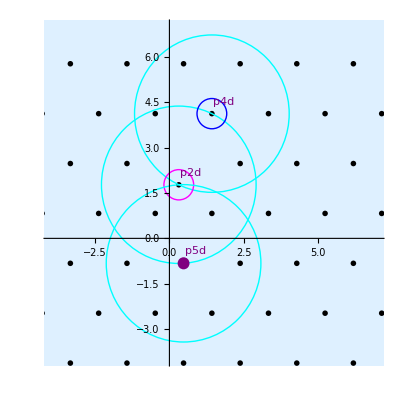

```mathematica
pnts288p2carr=Flatten[pnts288p2c⟦"pn"⟧,1];
p2d=pnts288p2carr⟦10 16+9⟧; (* Row 11, col. 9; Point to move *)
p4d=pnts288p2carr⟦11 16+9⟧; (* Row 12, col. 9; secondary shell center *)
p5d=pnts288p2carr⟦120+17⟧; (* By radius center *)
p288p2c=Show[plotPnts[pnts288p2c],
pntsc=Graphics[{Cyan,Circle[p2d,NHOPr],
Cyan,Circle[p4c,NHOPr],
Blue, Circle[p4c,0.5],
Magenta,Circle[p2d,0.5],
Cyan, Circle[ p5d,NHOPr ],
Purple, Circle[p5d, pnts288⟦"By"⟧],Disk[p5c,0.2],(* Center particle *)
Text["p2d",p2d+to],Text["p4d",p4d+to],Text["p5d",p5d+to]}],
PlotRange->{{-4,7},{-4,7}} ]
```

By definition, p2d is now moved to the edge of p4d’s NHOPr, and thus p4d has only five particles in its orbit. p2d now has p5d in its orbit, and so it has six particles. p5d has p2c, so it has seven. So by moving the one particle, we created a pair of dislocations.

##### Replicating the MD2 Experiment

The experiment moving a particle between two particles added energy of 0.01256 ϵ per particle. We can use Pdx to estimate that too.  In that scenario, we moved a particle up (y only) by 1.6547. This experiment was performed on a small system of 100 particles.

```mathematica
p5cfunc[0,1.6547]/100
```

0.0133502

That is a bit bigger than we saw.  It is likely that the initial motion was large enough that some energy was lost in the first few steps.

#### Moving Two Particles

A more likely scenario is if two particles were displaced toward each other, and thus the distance is halved (p2c would remain in p4c's NHOPr range).

rn2[]’s estimate of that is high:

```mathematica
rn2[EuclideanDistance[pip1,p2c],a79,5]
```

0.17873

That would also compare to the temperature (i.e., kinetic energy) required for that to be the average displacement.

```mathematica
2rn2[EuclideanDistance[pip1,p2c]/2,a79,5]
```

0.0507789

A somewhat lower energy would be moving vertically (so the two particles move directly toward each other).  p5c is two rows below p2c.

```mathematica
{p5c-p2c}
```

{{0,-3^(1/4) √(2 π)}}

```mathematica
EuclideanDistance[p5c,p2c]
```

3^(1/4) √(2 π)

p2c is only a small distance above p5c’s NHOPr.

```mathematica
d2=%-NHOPr
```

-((1+√3) √π)/(√2 3^(1/4))+3^(1/4) √(2 π)

```mathematica
N[%]
```

0.697141

```mathematica
2rn2[(EuclideanDistance[p5c,p2c]-NHOPr)/2,a79,5]
```

0.0470391

In a 256 particle system, this would amount to a small temperature increase.

```mathematica
%/256
```

0.000183746

p5c is particle number 137 and is located via the following:

```mathematica
{N[p5c],Floor[137/pnts288⟦"Nc"⟧+1],Mod[137,pnts288⟦"Nc"⟧], N[pnts288⟦"pn"⟧⟦9,9⟧]}
```

{{0.476156,-0.824727},9,9,{0.476156,-0.824727}}

```mathematica
pnts288p2p5c =pnts288; (* copy the array *)
pnts288p2p5c⟦"pn"⟧⟦11,9⟧=p2c - {0, d2/2}; (* replace p2c with moved coordinates *)
pnts288p2p5c⟦"pn"⟧⟦9,9⟧ = p5c + {0,d2/2}; (* replace p5c with moved coordinates *)
N[{pnts288p2p5c⟦"pn"⟧⟦9,9⟧,pnts288p2p5c⟦"pn"⟧⟦11,9⟧}]
```

{{0.476156,-0.476156},{0.476156,2.12561}}

Here is the plot.  Particles are now named with a “d” instead of “c.”

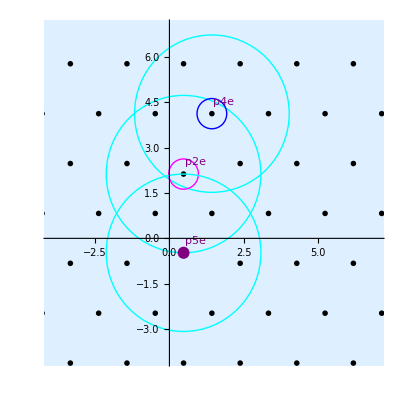

```mathematica
pnts288p2p5carr=Flatten[pnts288p2p5c⟦"pn"⟧,1];
p2e=pnts288p2p5carr⟦10 16+9⟧; (* Row 11, col. 9; Point to move *)
p4e=pnts288p2p5carr⟦11 16+9⟧; (* Row 12, col. 9; secondary shell center *)
p5e=pnts288p2p5carr⟦120+17⟧; (* By radius center *)
p288p2p5c=Show[plotPnts[pnts288p2p5c],
pntsc=Graphics[{Cyan,Circle[p2e,NHOPr],
Cyan,Circle[p4e,NHOPr],
Blue, Circle[p4e,0.5],
Magenta,Circle[p2e,0.5],
Cyan, Circle[ p5e,NHOPr ],
Purple, Circle[p5e, pnts288⟦"By"⟧],Disk[p5e,0.2],(* Center particle *)
Text["p2e",p2e+to],Text["p4e",p4e+to],Text["p5e",p5e+to]}],
PlotRange->{{-4,7},{-4,7}} ]
```

In this scenario, both p2e and p5e have seven particles in their NHOPr.

##### Finding an Energy Step

While testing the two particle dislocation in Julia, a few energy steps showed up in the total energy.  The per-particle magnitude  was 4.48×10^-8, so if it were just two particles in a 100 particle system, it would be 2.26×10^-6.

```mathematica
Solve[rn[x,5,3.5]==2.26 10^-6]
```

{{x→3.49917}}

```mathematica
rn[%[[1, All, 2]]⟦1⟧,5,3.5]
```

2.26×10^-6

We could also have gotten there directly:

```mathematica
(2.26 10^-6+rn[3.5,5])^(-1/5)
```

3.49917

That is a very small step inside the skin. At a time step of 0.01, the speed required would be

```mathematica
(7/2-3.499169695184254)/0.01
```

0.0830305

```mathematica
??rn
```

rn[r, n]=r^-n.
rn[r_, n_:5, Rskn_:3.5] respects the skin depth and causes the potential to be zero 
at the skin depth range Rskn.

rn[r_,n_]:=r^-n
 
rn[r_,n_:5,Rskn_:3.5]:=Piecewise[{{0,r≥Rskn},{rn[r,n]-rn[Rskn,n],True}}]

The maximum speed of the saved file was 0.809 (after another 904 steps), so that makes at least some sense.

### Spectral Processing

We process the temperature profiles to determine when the system is in equilibrium.  The current plan (started in late 2024 and still in use in December of ‘25) is to perform a 500-step block average and use those averages to form the key statistics (ke.mean.rs, ke.sd.rs, etc.).  The 500-step average was to eliminate the correlations that occur at short time intervals.

Each row of an MD2 data table has a specwidth recorded.  This is the fraction of the spectrum of the per-step kinetic energy occupied by 99.5% of the energy, usually just 2% to 5% of the entire spectrum. The spectrums are computed as averages with 50% overlap and Hanning windows and are de-trended first. The default (always used) is a 4,096 point FFT,

### Application of the Virial Theorem

The Virial Theorem for r^-n potentials states that the total kinetic energy is related to the total potential energy as 2⟨K_T⟩=-n⟨U_T⟩, where the angle brackets denote averages. Combine this with the pressure equation P = ρ⟨K_T⟩(1+(n⟨U_T⟩)/(2⟨K_T⟩)), where ρ is the density, the pressure becomes simply 2ρ⟨K_T⟩.  This is evidently wrong, as was shown by [Louwerse2006] in three dimensions.

```mathematica
AbsoluteTime[] - MD2StartTime
```

45.261606

References

[Aurenhammer1991] F. Aurenhammer, “Voronoi diagrams—a survey of a fundamental geometric data structure,” ACM Comput. Surv., vol. 23, no. 3, pp. 345–405, Sept. 1991, doi: 10.1145/116873.116880.

[Awile2012] O. Awile, F. Büyükkeçeci, S. Reboux, and I. F. Sbalzarini, “Fast neighbor lists for adaptive-resolution particle simulations,” Computer Physics Communications, vol. 183, no. 5, pp. 1073–1081, May 2012, doi: 10.1016/j.cpc.2012.01.003.

[Fukshansky2011] L. Fukshansky, “Revisiting the hexagonal lattice: on optimal lattice circle packing,” Elem. Math., vol. 66, no. 1, pp. 1–9, Jan. 2011, doi: 10.4171/em/163.

[Gross2019] J. Gross, M. Köster, and A. Krüger, “Fast and Efficient Nearest Neighbor Search for Particle Simulations,” Computer Graphics and Visual Computing (CGVC), p. 9 pages, 2019, doi: 10.2312/CGVC.20191258.

[Halperin1978] B. I. Halperin and D. R. Nelson, “Theory of Two-Dimensional Melting,” Phys. Rev. Lett., vol. 41, no. 2, pp. 121–124, July 1978, doi: 10.1103/PhysRevLett.41.121.

[Kapfer2015] S. C. Kapfer and W. Krauth, “Two-Dimensional Melting: From Liquid-Hexatic Coexistence to Continuous Transitions,” Phys. Rev. Lett., vol. 114, no. 3, p. 035702, Jan. 2015, doi: 10.1103/PhysRevLett.114.035702.

[Keim2007] P. Keim, G. Maret, and H. H. von Grünberg, “Frank’s constant in the hexatic phase,” Phys. Rev. E, vol. 75, no. 3, p. 031402, Mar. 2007, doi: 10.1103/PhysRevE.75.031402.

[Kim2025] J.-H. Kim and J. Lee, “Scalable and rapid nearest neighbor particle search using adaptive disk sector,” PLOS ONE, vol. 20, no. 3, p. e0311163, Mar. 2025, doi: 10.1371/journal.pone.0311163.

[Louwerse2006] Manuel J. Louwerse and Evert Jan Baerends, “Calculation of pressure in case of periodic boundary conditions,” Chemical Physics Letters 421 (2006) 138–141

[Reif1965] F. Reif, Fundamentals of Statistical and Thermal Physics. New York, NY: McGraw-Hill, 1965.

[Swope1982] W. C. Swope, H. C. Andersen, P. H. Berens, and K. R. Wilson, "A computer simulation method for the calculation of equilibrium constants for the formation of physical clusters of molecules: Application to small water clusters," J. Chem. Phys., vol. 76, no. 1, pp. 637–649, Jan. 1982, doi: 10.1063/1.442716.

[Toledano2021] Ó. Toledano, M. Pancorbo, J. E. Alvarellos, and Ó. Gálvez, “Melting in two-dimensional systems: Characterizing continuous and first-order transitions,” Phys. Rev. B, vol. 103, no. 9, p. 094107, Mar. 2021, doi: 10.1103/PhysRevB.103.094107.

[Verlet1967] L. Verlet, “Computer ‘Experiments’ on Classical Fluids. I. Thermodynamical Properties of Lennard-Jones Molecules,” Phys. Rev., vol. 159, no. 1, pp. 98–103, 1967, doi: 10.1103/PhysRev.159.98.